```mathematica
response=Import["https://evetycoon.com/api/v1/market/stats/10000002/44992"]
```

{buyVolume→552781,sellVolume→380183,buyOrders→371,sellOrders→165,buyOutliers→99,sellOutliers→8,buyThreshold→504100.,sellThreshold→5.197×10^7,buyAvgFivePercent→5.03055×10^6,sellAvgFivePercent→5.22332×10^6,maxBuy→5.041×10^6,minSell→5.197×10^6}

```mathematica
NetModel["NewModel"]
```

NetModel::nonetmodel2: No model with name NewModel could be found. Did you mean Ademxapp Model A1 Trained on ADE20K Data?

$Failed

```mathematica
(* List of Key-value pairs, should be time->stock value *)
trainingData={1->1.9,2->4.1,3->6.0,4->8.1}

net=NetChain[{ElementwiseLayer["ELU"], ElementwiseLayer["ELU"], ElementwiseLayer["ELU"], LinearLayer[]}]
net= NetTrain[net, trainingData]

(* Call the net with a specific key, predicts value *)
net[2]
```

{1→1.9,2→4.1,3→6.,4→8.1}

NetChain[…]

NetChain[…]

4.00181

NetChain[…]

2.05652

```mathematica
net[1]
net1[1]
```

NetChain::nfspec: Cannot evaluate net: input of first layer is not fully specified.

$Failed

1.9507

{buyVolume→543807,sellVolume→379311,buyOrders→363,sellOrders→165,buyOutliers→99,sellOutliers→8,buyThreshold→503200.,sellThreshold→5.197×10^7,buyAvgFivePercent→5.02598×10^6,sellAvgFivePercent→5.22507×10^6,maxBuy→5.032×10^6,minSell→5.197×10^6}

```mathematica
Import["https://evetycoon.com/api/v1/market/history/10000002/44992"]
```

```mathematica
c=Import["https://evetycoon.com/api/v1/market/history/10000002/44992"]
```

```mathematica
C1=c[[1]]
```

{date→1572566400000,regionId→10000002,typeId→44992,average→3.47012×10^6,highest→3.59011×10^6,lowest→3.4614×10^6,orderCount→2168,volume→1153189}

```mathematica
data={}
```

{}

```mathematica
data=Values[#[[1]]]->Values[#[[4]]]&/@c
```

{1572566400000→3.47012×10^6,1572652800000→3.456×10^6,1572739200000→3.44944×10^6,1572825600000→3.47×10^6,1572912000000→3.45731×10^6,1572998400000→3.46×10^6,1573084800000→3.465×10^6,1573171200000→3.46033×10^6,1573257600000→3.45031×10^6,1573344000000→3.43167×10^6,1573430400000→3.44089×10^6,1573516800000→3.54285×10^6,1573603200000→3.4378×10^6,1573689600000→3.43274×10^6,1573776000000→3.4303×10^6,1573862400000→3.41201×10^6,1573948800000→3.40401×10^6,1574035200000→3.4037×10^6,1574121600000→3.40233×10^6,1574208000000→3.382×10^6,1574294400000→3.392×10^6,1574380800000→3.37703×10^6,1574467200000→3.36062×10^6,1574553600000→3.3462×10^6,1574640000000→3.375×10^6,1574726400000→3.35×10^6,1574812800000→3.44697×10^6,1574899200000→3.3×10^6,1574985600000→3.21315×10^6,1575072000000→3.252×10^6,1575158400000→3.2935×10^6,1575244800000→3.2752×10^6,1575331200000→3.3059×10^6,1575417600000→3.3073×10^6,1575504000000→3.30102×10^6,1575590400000→3.28302×10^6,1575676800000→3.2784×10^6,1575763200000→3.27207×10^6,1575849600000→3.31001×10^6,1575936000000→3.3637×10^6,1576022400000→3.3602×10^6,1576108800000→3.317×10^6,1576195200000→3.30761×10^6,1576281600000→3.29101×10^6,1576368000000→3.26815×10^6,1576454400000→3.25×10^6,1576540800000→3.2431×10^6,1576627200000→3.24009×10^6,1576713600000→3.21016×10^6,1576800000000→3.2046×10^6,1576886400000→3.171×10^6,1576972800000→3.1669×10^6,1577059200000→3.18×10^6,1577145600000→3.2102×10^6,1577232000000→3.39998×10^6,1577318400000→3.41127×10^6,1577404800000→3.3713×10^6,1577491200000→3.28×10^6,1577577600000→3.25209×10^6,1577664000000→3.25×10^6,1577750400000→3.23006×10^6,1577836800000→3.2101×10^6,1577923200000→3.18622×10^6,1578009600000→3.20001×10^6,1578096000000→3.19931×10^6,1578182400000→3.1922×10^6,1578268800000→3.1854×10^6,1578355200000→3.2×10^6,1578441600000→3.205×10^6,1578528000000→3.20121×10^6,1578614400000→3.20199×10^6,1578700800000→3.19171×10^6,1578787200000→3.2×10^6,1578873600000→3.195×10^6,1578960000000→3.19211×10^6,1579046400000→3.1972×10^6,1579132800000→3.1942×10^6,1579219200000→3.1931×10^6,1579305600000→3.19104×10^6,1579392000000→3.19635×10^6,1579478400000→3.20405×10^6,1579564800000→3.202×10^6,1579651200000→3.20762×10^6,1579737600000→3.21208×10^6,1579824000000→3.22594×10^6,1579910400000→3.28×10^6,1579996800000→3.27401×10^6,1580083200000→3.27621×10^6,1580169600000→3.29×10^6,1580256000000→3.2972×10^6,1580342400000→3.29525×10^6,1580428800000→3.2965×10^6,1580515200000→3.28061×10^6,1580601600000→3.28022×10^6,1580688000000→3.27955×10^6,1580774400000→3.27105×10^6,1580860800000→3.28603×10^6,1580947200000→3.276×10^6,1581033600000→3.26831×10^6,1581120000000→3.26403×10^6,1581206400000→3.2585×10^6,1581292800000→3.25614×10^6,1581379200000→3.263×10^6,1581465600000→3.30001×10^6,1581552000000→3.28051×10^6,1581638400000→3.27504×10^6,1581724800000→3.28471×10^6,1581811200000→3.27606×10^6,1581897600000→3.27814×10^6,1581984000000→3.28501×10^6,1582070400000→3.28312×10^6,1582156800000→3.2845×10^6,1582243200000→3.2803×10^6,1582329600000→3.25652×10^6,1582416000000→3.24601×10^6,1582502400000→3.35008×10^6,1582588800000→3.29501×10^6,1582675200000→3.28607×10^6,1582761600000→3.28606×10^6,1582848000000→3.20012×10^6,1582934400000→3.19002×10^6,1583020800000→3.18501×10^6,1583107200000→3.19341×10^6,1583193600000→3.206×10^6,1583280000000→3.22251×10^6,1583366400000→3.21706×10^6,1583452800000→3.19815×10^6,1583539200000→3.20025×10^6,1583625600000→3.20404×10^6,1583712000000→3.22016×10^6,1583798400000→3.22703×10^6,1583884800000→3.219×10^6,1583971200000→3.221×10^6,1584057600000→3.22×10^6,1584144000000→3.212×10^6,1584230400000→3.206×10^6,1584316800000→3.201×10^6,1584403200000→3.196×10^6,1584489600000→3.186×10^6,1584576000000→3.176×10^6,1584662400000→3.151×10^6,1584748800000→3.101×10^6,1584835200000→3.124×10^6,1584921600000→3.15×10^6,1585008000000→3.15×10^6,1585094400000→3.136×10^6,1585180800000→3.135×10^6,1585267200000→3.126×10^6,1585353600000→3.093×10^6,1585440000000→3.099×10^6,1585526400000→3.074×10^6,1585612800000→3.056×10^6,1585699200000→3.013×10^6,1585785600000→2.913×10^6,1585872000000→2.9×10^6,1585958400000→2.958×10^6,1586044800000→2.977×10^6,1586131200000→2.962×10^6,1586217600000→2.915×10^6,1586304000000→2.903×10^6,1586390400000→2.887×10^6,1586476800000→3.135×10^6,1586563200000→3.173×10^6,1586649600000→3.075×10^6,1586736000000→2.971×10^6,1586822400000→2.949×10^6,1586908800000→2.871×10^6,1586995200000→2.778×10^6,1587081600000→2.74×10^6,1587168000000→2.72×10^6,1587254400000→2.716×10^6,1587340800000→2.745×10^6,1587427200000→2.779×10^6,1587513600000→2.796×10^6,1587600000000→2.768×10^6,1587686400000→2.73×10^6,1587772800000→2.681×10^6,1587859200000→2.672×10^6,1587945600000→2.66×10^6,1588032000000→2.644×10^6,1588118400000→2.608×10^6,1588204800000→2.58×10^6,1588291200000→2.573×10^6,1588377600000→2.593×10^6,1588464000000→2.583×10^6,1588550400000→2.575×10^6,1588636800000→2.608×10^6,1588723200000→2.594×10^6,1588809600000→2.592×10^6,1588896000000→2.579×10^6,1588982400000→2.55×10^6,1589068800000→2.556×10^6,1589155200000→2.578×10^6,1589241600000→2.564×10^6,1589328000000→2.547×10^6,1589414400000→2.526×10^6,1589500800000→2.535×10^6,1589587200000→2.5×10^6,1589673600000→2.465×10^6,1589760000000→2.451×10^6,1589846400000→2.468×10^6,1589932800000→2.476×10^6,1590019200000→2.49×10^6,1590105600000→2.498×10^6,1590192000000→2.478×10^6,1590278400000→2.481×10^6,1590364800000→2.609×10^6,1590451200000→2.806×10^6,1590537600000→2.673×10^6,1590624000000→2.648×10^6,1590710400000→2.516×10^6,1590796800000→2.492×10^6,1590883200000→2.506×10^6,1590969600000→2.526×10^6,1591056000000→2.531×10^6,1591142400000→2.542×10^6,1591228800000→2.542×10^6,1591315200000→2.531×10^6,1591401600000→2.521×10^6,1591488000000→2.516×10^6,1591574400000→2.545×10^6,1591660800000→2.545×10^6,1591747200000→2.553×10^6,1591833600000→2.558×10^6,1591920000000→2.705×10^6,1592006400000→2.752×10^6,1592092800000→2.757×10^6,1592179200000→2.612×10^6,1592265600000→2.61×10^6,1592352000000→2.571×10^6,1592438400000→2.581×10^6,1592524800000→2.583×10^6,1592611200000→2.567×10^6,1592697600000→2.567×10^6,1592784000000→2.563×10^6,1592870400000→2.55×10^6,1592956800000→2.558×10^6,1593043200000→2.555×10^6,1593129600000→2.55×10^6,1593216000000→2.554×10^6,1593302400000→2.544×10^6,1593388800000→2.551×10^6,1593475200000→2.523×10^6,1593561600000→2.511×10^6,1593648000000→2.51×10^6,1593734400000→2.503×10^6,1593820800000→2.479×10^6,1593907200000→2.451×10^6,1593993600000→2.477×10^6,1594080000000→2.46×10^6,1594166400000→2.463×10^6,1594252800000→2.477×10^6,1594339200000→2.48×10^6,1594425600000→2.487×10^6,1594512000000→2.489×10^6,1594598400000→2.486×10^6,1594684800000→2.49×10^6,1594771200000→2.49×10^6,1594857600000→2.48×10^6,1594944000000→2.48×10^6,1595030400000→2.483×10^6,1595116800000→2.485×10^6,1595203200000→2.495×10^6,1595289600000→2.492×10^6,1595376000000→2.495×10^6,1595462400000→2.492×10^6,1595548800000→2.491×10^6,1595635200000→2.494×10^6,1595721600000→2.494×10^6,1595808000000→2.5×10^6,1595894400000→2.496×10^6,1595980800000→2.504×10^6,1596067200000→2.503×10^6,1596153600000→2.495×10^6,1596240000000→2.491×10^6,1596326400000→2.496×10^6,1596412800000→2.5×10^6,1596499200000→2.495×10^6,1596585600000→2.5×10^6,1596672000000→2.495×10^6,1596758400000→2.499×10^6,1596844800000→2.499×10^6,1596931200000→2.515×10^6,1597017600000→2.508×10^6,1597104000000→2.513×10^6,1597190400000→2.531×10^6,1597276800000→2.523×10^6,1597363200000→2.533×10^6,1597449600000→2.534×10^6,1597536000000→2.541×10^6,1597622400000→2.543×10^6,1597708800000→2.544×10^6,1597795200000→2.552×10^6,1597881600000→2.556×10^6,1597968000000→2.548×10^6,1598054400000→2.544×10^6,1598140800000→2.554×10^6,1598227200000→2.557×10^6,1598313600000→2.57×10^6,1598400000000→2.582×10^6,1598486400000→2.597×10^6,1598572800000→2.799×10^6,1598659200000→2.73×10^6,1598745600000→2.728×10^6,1598832000000→2.632×10^6,1598918400000→2.615×10^6,1599004800000→2.631×10^6,1599091200000→2.628×10^6,1599177600000→2.626×10^6,1599264000000→2.623×10^6,1599350400000→2.613×10^6,1599436800000→2.618×10^6,1599523200000→2.615×10^6,1599609600000→2.61×10^6,1599696000000→2.602×10^6,1599782400000→2.6×10^6,1599868800000→2.6×10^6,1599955200000→2.612×10^6,1600041600000→2.617×10^6,1600128000000→2.626×10^6,1600214400000→2.615×10^6,1600300800000→2.612×10^6,1600387200000→2.611×10^6,1600473600000→2.607×10^6,1600560000000→2.608×10^6,1600646400000→2.623×10^6,1600732800000→2.612×10^6,1600819200000→2.607×10^6,1600905600000→2.61×10^6,1600992000000→2.607×10^6,1601078400000→2.611×10^6,1601164800000→2.607×10^6,1601251200000→2.613×10^6,1601337600000→2.614×10^6,1601424000000→2.618×10^6,1601510400000→2.615×10^6,1601596800000→2.625×10^6,1601683200000→2.626×10^6,1601769600000→2.634×10^6,1601856000000→2.66×10^6,1601942400000→2.67×10^6,1602028800000→2.726×10^6,1602115200000→2.762×10^6,1602201600000→2.787×10^6,1602288000000→2.72×10^6,1602374400000→2.688×10^6,1602460800000→2.692×10^6,1602547200000→2.689×10^6,1602633600000→2.698×10^6,1602720000000→2.696×10^6,1602806400000→2.699×10^6,1602892800000→2.697×10^6,1602979200000→2.693×10^6,1603065600000→2.694×10^6,1603152000000→2.707×10^6,1603238400000→2.7×10^6,1603324800000→2.701×10^6,1603411200000→2.713×10^6,1603497600000→2.706×10^6,1603584000000→2.707×10^6,1603670400000→2.705×10^6,1603756800000→2.71×10^6,1603843200000→2.709×10^6,1603929600000→2.706×10^6,1604016000000→2.713×10^6,1604102400000→2.687×10^6,1604188800000→2.691×10^6,1604275200000→2.693×10^6,1604361600000→2.696×10^6,1604448000000→2.706×10^6,1604534400000→2.697×10^6,1604620800000→2.694×10^6,1604707200000→2.692×10^6,1604793600000→2.693×10^6,1604880000000→2.697×10^6,1604966400000→2.7×10^6,1605052800000→2.7×10^6,1605139200000→2.709×10^6,1605225600000→2.703×10^6,1605312000000→2.702×10^6,1605398400000→2.7×10^6,1605484800000→2.704×10^6,1605571200000→2.706×10^6,1605657600000→2.718×10^6,1605744000000→2.72×10^6,1605830400000→2.716×10^6,1605916800000→2.709×10^6,1606003200000→2.717×10^6,1606089600000→2.726×10^6,1606176000000→2.751×10^6,1606262400000→2.748×10^6,1606348800000→2.63×10^6,1606435200000→2.64×10^6,1606521600000→2.688×10^6,1606608000000→2.686×10^6,1606694400000→2.711×10^6,1606780800000→2.708×10^6,1606867200000→2.696×10^6,1606953600000→2.696×10^6,1607040000000→2.691×10^6,1607126400000→2.686×10^6,1607212800000→2.682×10^6,1607299200000→2.688×10^6,1607385600000→2.683×10^6,1607472000000→2.68×10^6,1607558400000→2.697×10^6,1607644800000→2.679×10^6,1607731200000→2.672×10^6,1607817600000→2.674×10^6,1607904000000→2.672×10^6,1607990400000→2.664×10^6,1608076800000→2.666×10^6,1608163200000→2.661×10^6,1608249600000→2.664×10^6,1608336000000→2.657×10^6,1608422400000→2.642×10^6,1608508800000→2.642×10^6,1608595200000→2.65×10^6,1608681600000→2.646×10^6,1608768000000→2.8×10^6,1608854400000→2.819×10^6,1608940800000→2.77×10^6,1609027200000→2.657×10^6,1609113600000→2.651×10^6,1609200000000→2.647×10^6,1609286400000→2.643×10^6,1609372800000→2.638×10^6,1609459200000→2.606×10^6,1609545600000→2.56×10^6,1609632000000→2.552×10^6,1609718400000→2.559×10^6,1609804800000→2.557×10^6,1609891200000→2.546×10^6,1609977600000→2.541×10^6,1610064000000→2.533×10^6,1610150400000→2.492×10^6,1610236800000→2.49×10^6,1610323200000→2.512×10^6,1610409600000→2.5×10^6,1610496000000→2.531×10^6,1610582400000→2.508×10^6,1610668800000→2.501×10^6,1610755200000→2.499×10^6,1610841600000→2.503×10^6,1610928000000→2.505×10^6,1611014400000→2.5×10^6,1611100800000→2.501×10^6,1611187200000→2.498×10^6,1611273600000→2.49×10^6,1611360000000→2.486×10^6,1611446400000→2.481×10^6,1611532800000→2.481×10^6,1611619200000→2.484×10^6,1611705600000→2.473×10^6,1611792000000→2.472×10^6,1611878400000→2.471×10^6,1611964800000→2.466×10^6,1612051200000→2.455×10^6,1612137600000→2.475×10^6,1612224000000→2.459×10^6,1612310400000→2.455×10^6,1612396800000→2.446×10^6,1612483200000→2.442×10^6,1612569600000→2.439×10^6,1612656000000→2.438×10^6,1612742400000→2.46×10^6,1612828800000→2.445×10^6,1612915200000→2.444×10^6,1613001600000→2.441×10^6,1613088000000→2.438×10^6,1613174400000→2.43×10^6,1613260800000→2.427×10^6,1613347200000→2.414×10^6,1613433600000→2.413×10^6,1613520000000→2.412×10^6,1613606400000→2.41×10^6,1613692800000→2.41×10^6,1613779200000→2.4×10^6,1613865600000→2.408×10^6,1613952000000→2.415×10^6,1614038400000→2.418×10^6,1614124800000→2.421×10^6,1614211200000→2.42×10^6,1614297600000→2.402×10^6,1614384000000→2.362×10^6,1614470400000→2.335×10^6,1614556800000→2.334×10^6,1614643200000→2.338×10^6,1614729600000→2.337×10^6,1614816000000→2.341×10^6,1614902400000→2.343×10^6,1614988800000→2.331×10^6,1615075200000→2.322×10^6,1615161600000→2.33×10^6,1615248000000→2.324×10^6,1615334400000→2.318×10^6,1615420800000→2.317×10^6,1615507200000→2.315×10^6,1615593600000→2.301×10^6,1615680000000→2.298×10^6,1615766400000→2.305×10^6,1615852800000→2.304×10^6,1615939200000→2.291×10^6,1616025600000→2.245×10^6,1616112000000→2.223×10^6,1616198400000→2.201×10^6,1616284800000→2.199×10^6,1616371200000→2.204×10^6,1616457600000→2.209×10^6,1616544000000→2.24×10^6,1616630400000→2.244×10^6,1616716800000→2.225×10^6,1616803200000→2.198×10^6,1616889600000→2.195×10^6,1616976000000→2.195×10^6,1617062400000→2.208×10^6,1617148800000→2.219×10^6,1617235200000→2.2×10^6,1617321600000→2.2×10^6,1617408000000→2.197×10^6,1617494400000→2.208×10^6,1617580800000→2.239×10^6,1617667200000→2.22×10^6,1617753600000→2.237×10^6,1617840000000→2.255×10^6,1617926400000→2.264×10^6,1618012800000→2.3×10^6,1618099200000→2.3×10^6,1618185600000→2.326×10^6,1618272000000→2.361×10^6,1618358400000→2.405×10^6,1618444800000→2.394×10^6,1618531200000→2.386×10^6,1618617600000→2.37×10^6,1618704000000→2.332×10^6,1618790400000→2.406×10^6,1618876800000→2.388×10^6,1618963200000→2.367×10^6,1619049600000→2.366×10^6,1619136000000→2.346×10^6,1619222400000→2.298×10^6,1619308800000→2.297×10^6,1619395200000→2.296×10^6,1619481600000→2.3×10^6,1619568000000→2.304×10^6,1619654400000→2.308×10^6,1619740800000→2.305×10^6,1619827200000→2.301×10^6,1619913600000→2.309×10^6,1620000000000→2.298×10^6,1620086400000→2.296×10^6,1620172800000→2.293×10^6,1620259200000→2.306×10^6,1620345600000→2.31×10^6,1620432000000→2.314×10^6,1620518400000→2.313×10^6,1620604800000→2.38×10^6,1620691200000→2.401×10^6,1620777600000→2.411×10^6,1620864000000→2.438×10^6,1620950400000→2.398×10^6,1621036800000→2.341×10^6,1621123200000→2.377×10^6,1621209600000→2.406×10^6,1621296000000→2.421×10^6,1621382400000→2.405×10^6,1621468800000→2.374×10^6,1621555200000→2.366×10^6,1621641600000→2.346×10^6,1621728000000→2.375×10^6,1621814400000→2.386×10^6,1621900800000→2.382×10^6,1621987200000→2.365×10^6,1622073600000→2.385×10^6,1622160000000→2.381×10^6,1622246400000→2.417×10^6,1622332800000→2.39×10^6,1622419200000→2.392×10^6,1622505600000→2.402×10^6,1622592000000→2.397×10^6,1622678400000→2.391×10^6,1622764800000→2.39×10^6,1622851200000→2.397×10^6,1622937600000→2.405×10^6,1623024000000→2.415×10^6,1623110400000→2.451×10^6,1623196800000→2.441×10^6,1623283200000→2.504×10^6,1623369600000→2.497×10^6,1623456000000→2.504×10^6,1623542400000→2.472×10^6,1623628800000→2.476×10^6,1623715200000→2.489×10^6,1623801600000→2.479×10^6,1623888000000→2.484×10^6,1623974400000→2.478×10^6,1624060800000→2.472×10^6,1624147200000→2.474×10^6,1624233600000→2.481×10^6,1624320000000→2.491×10^6,1624406400000→2.5×10^6,1624492800000→2.502×10^6,1624579200000→2.5×10^6,1624665600000→2.51×10^6,1624752000000→2.56×10^6,1624838400000→2.548×10^6,1624924800000→2.552×10^6,1625011200000→2.566×10^6,1625097600000→2.57×10^6,1625184000000→2.564×10^6,1625270400000→2.559×10^6,1625356800000→2.602×10^6,1625443200000→2.621×10^6,1625529600000→2.613×10^6,1625616000000→2.726×10^6,1625702400000→2.693×10^6,1625788800000→2.689×10^6,1625875200000→2.664×10^6,1625961600000→2.649×10^6,1626048000000→2.7×10^6,1626134400000→2.71×10^6,1626220800000→2.698×10^6,1626307200000→2.7×10^6,1626393600000→2.696×10^6,1626480000000→2.686×10^6,1626566400000→2.693×10^6,1626652800000→2.687×10^6,1626739200000→2.667×10^6,1626825600000→2.673×10^6,1626912000000→2.65×10^6,1626998400000→2.634×10^6,1627084800000→2.618×10^6,1627171200000→2.581×10^6,1627257600000→2.613×10^6,1627344000000→2.72×10^6,1627430400000→2.72×10^6,1627516800000→2.721×10^6,1627603200000→2.72×10^6,1627689600000→2.644×10^6,1627776000000→2.691×10^6,1627862400000→2.696×10^6,1627948800000→2.71×10^6,1628035200000→2.688×10^6,1628121600000→2.681×10^6,1628208000000→2.665×10^6,1628294400000→2.633×10^6,1628380800000→2.626×10^6,1628467200000→2.636×10^6,1628553600000→2.631×10^6,1628640000000→2.616×10^6,1628726400000→2.616×10^6,1628812800000→2.599×10^6,1628899200000→2.589×10^6,1628985600000→2.561×10^6,1629072000000→2.591×10^6,1629158400000→2.575×10^6,1629244800000→2.565×10^6,1629331200000→2.551×10^6,1629417600000→2.556×10^6,1629504000000→2.559×10^6,1629590400000→2.58×10^6,1629676800000→2.592×10^6,1629763200000→2.563×10^6,1629849600000→2.587×10^6,1629936000000→2.59×10^6,1630022400000→2.586×10^6,1630108800000→2.58×10^6,1630195200000→2.579×10^6,1630281600000→2.579×10^6,1630368000000→2.587×10^6,1630454400000→2.588×10^6,1630540800000→2.591×10^6,1630627200000→2.585×10^6,1630713600000→2.59×10^6,1630800000000→2.592×10^6,1630886400000→2.598×10^6,1630972800000→2.615×10^6,1631059200000→2.621×10^6,1631145600000→2.633×10^6,1631232000000→2.641×10^6,1631318400000→2.637×10^6,1631404800000→2.634×10^6,1631491200000→2.643×10^6,1631577600000→2.654×10^6,1631664000000→2.656×10^6,1631750400000→2.662×10^6,1631836800000→2.698×10^6,1631923200000→2.694×10^6,1632009600000→2.7×10^6,1632096000000→2.71×10^6,1632182400000→2.746×10^6,1632268800000→2.743×10^6,1632355200000→2.729×10^6,1632441600000→2.731×10^6,1632528000000→2.726×10^6,1632614400000→2.737×10^6,1632700800000→2.757×10^6,1632787200000→2.771×10^6,1632873600000→2.791×10^6,1632960000000→2.794×10^6,1633046400000→2.802×10^6,1633132800000→2.778×10^6,1633219200000→2.79×10^6,1633305600000→2.796×10^6,1633392000000→2.763×10^6,1633478400000→2.771×10^6,1633564800000→2.779×10^6,1633651200000→2.78×10^6,1633737600000→2.776×10^6,1633824000000→2.783×10^6,1633910400000→2.793×10^6,1633996800000→2.808×10^6,1634083200000→2.835×10^6,1634169600000→2.829×10^6,1634256000000→2.83×10^6,1634342400000→2.83×10^6,1634428800000→2.832×10^6,1634515200000→2.832×10^6,1634601600000→2.846×10^6,1634688000000→2.891×10^6,1634774400000→2.945×10^6,1634860800000→2.93×10^6,1634947200000→2.952×10^6,1635033600000→2.955×10^6,1635120000000→2.94×10^6,1635206400000→2.943×10^6,1635292800000→2.938×10^6,1635379200000→2.942×10^6,1635465600000→2.924×10^6,1635552000000→2.855×10^6,1635638400000→2.845×10^6,1635724800000→2.84×10^6,1635811200000→2.841×10^6,1635897600000→2.882×10^6,1635984000000→2.91×10^6,1636070400000→2.871×10^6,1636156800000→2.9×10^6,1636243200000→2.906×10^6,1636329600000→2.907×10^6,1636416000000→2.98×10^6,1636502400000→2.953×10^6,1636588800000→2.951×10^6,1636675200000→2.932×10^6,1636761600000→2.929×10^6,1636848000000→2.914×10^6,1636934400000→2.926×10^6,1637020800000→2.908×10^6,1637107200000→2.895×10^6,1637193600000→2.891×10^6,1637280000000→2.857×10^6,1637366400000→2.848×10^6,1637452800000→2.851×10^6,1637539200000→2.857×10^6,1637625600000→2.856×10^6,1637712000000→2.857×10^6,1637798400000→2.802×10^6,1637884800000→2.755×10^6,1637971200000→2.781×10^6,1638057600000→2.801×10^6,1638144000000→2.794×10^6,1638230400000→2.786×10^6,1638316800000→2.778×10^6,1638403200000→2.784×10^6,1638489600000→2.802×10^6,1638576000000→2.78×10^6,1638662400000→2.781×10^6,1638748800000→2.792×10^6,1638835200000→2.767×10^6,1638921600000→2.785×10^6,1639008000000→2.767×10^6,1639094400000→2.768×10^6,1639180800000→2.764×10^6,1639267200000→2.78×10^6,1639353600000→2.767×10^6,1639440000000→2.76×10^6,1639526400000→2.759×10^6,1639612800000→2.766×10^6,1639699200000→2.76×10^6,1639785600000→2.752×10^6,1639872000000→2.751×10^6,1639958400000→2.775×10^6,1640044800000→2.768×10^6,1640131200000→2.929×10^6,1640217600000→2.913×10^6,1640304000000→2.809×10^6,1640390400000→2.786×10^6,1640476800000→2.763×10^6,1640563200000→2.775×10^6,1640649600000→2.777×10^6,1640736000000→2.767×10^6,1640822400000→2.765×10^6,1640908800000→2.758×10^6,1640995200000→2.752×10^6,1641081600000→2.746×10^6,1641168000000→2.781×10^6,1641254400000→2.776×10^6,1641340800000→2.756×10^6,1641427200000→2.754×10^6,1641513600000→2.759×10^6,1641600000000→2.735×10^6,1641686400000→2.739×10^6,1641772800000→2.748×10^6,1641859200000→2.739×10^6,1641945600000→2.736×10^6,1642032000000→2.742×10^6,1642118400000→2.752×10^6,1642204800000→2.746×10^6,1642291200000→2.75×10^6,1642377600000→2.747×10^6,1642464000000→2.751×10^6,1642550400000→2.754×10^6,1642636800000→2.75×10^6,1642723200000→2.749×10^6,1642809600000→2.75×10^6,1642896000000→2.75×10^6,1642982400000→2.747×10^6,1643068800000→2.755×10^6,1643155200000→2.755×10^6,1643241600000→2.749×10^6,1643328000000→2.743×10^6,1643414400000→2.817×10^6,1643500800000→2.785×10^6,1643587200000→2.8×10^6,1643673600000→2.786×10^6,1643760000000→2.785×10^6,1643846400000→2.768×10^6,1643932800000→2.763×10^6,1644019200000→2.758×10^6,1644105600000→2.753×10^6,1644192000000→2.776×10^6,1644278400000→2.759×10^6,1644364800000→2.762×10^6,1644451200000→2.771×10^6,1644537600000→2.766×10^6,1644624000000→2.78×10^6,1644710400000→2.785×10^6,1644796800000→2.784×10^6,1644883200000→2.795×10^6,1644969600000→2.797×10^6,1645056000000→2.796×10^6,1645142400000→2.805×10^6,1645228800000→2.816×10^6,1645315200000→2.816×10^6,1645401600000→2.808×10^6,1645488000000→2.804×10^6,1645574400000→2.81×10^6,1645660800000→2.796×10^6,1645747200000→2.786×10^6,1645833600000→2.92×10^6,1645920000000→2.982×10^6,1646006400000→2.98×10^6,1646092800000→2.867×10^6,1646179200000→2.802×10^6,1646265600000→2.802×10^6,1646352000000→2.999×10^6,1646438400000→3.064×10^6,1646524800000→3.01×10^6,1646611200000→2.902×10^6,1646697600000→2.946×10^6,1646784000000→2.928×10^6,1646870400000→2.898×10^6,1646956800000→2.894×10^6,1647043200000→2.87×10^6,1647129600000→2.905×10^6,1647216000000→2.907×10^6,1647302400000→2.927×10^6,1647388800000→2.972×10^6,1647475200000→2.991×10^6,1647561600000→2.99×10^6,1647648000000→2.966×10^6,1647734400000→2.98×10^6,1647820800000→2.999×10^6,1647907200000→3.095×10^6,1647993600000→3.008×10^6,1648080000000→3.007×10^6,1648166400000→3.006×10^6,1648252800000→3.012×10^6,1648339200000→3.008×10^6,1648425600000→3.005×10^6,1648512000000→3.005×10^6,1648598400000→2.995×10^6,1648684800000→2.977×10^6,1648771200000→2.931×10^6,1648857600000→2.91×10^6,1648944000000→2.911×10^6,1649030400000→2.906×10^6,1649116800000→2.918×10^6,1649203200000→2.907×10^6,1649289600000→2.956×10^6,1649376000000→2.903×10^6,1649462400000→2.901×10^6,1649548800000→2.904×10^6,1649635200000→2.911×10^6,1649721600000→2.889×10^6,1649808000000→2.9×10^6,1649894400000→2.902×10^6,1649980800000→2.894×10^6,1650067200000→2.9×10^6,1650153600000→2.9×10^6,1650240000000→2.897×10^6,1650326400000→2.892×10^6,1650412800000→2.904×10^6,1650499200000→2.95×10^6,1650585600000→3.447×10^6,1650672000000→3.545×10^6,1650758400000→3.37×10^6,1650844800000→3.4×10^6,1650931200000→3.3×10^6,1651017600000→3.182×10^6,1651104000000→3.1×10^6,1651190400000→3.085×10^6,1651276800000→3.09×10^6,1651363200000→3.087×10^6,1651449600000→3.101×10^6,1651536000000→3.225×10^6,1651622400000→3.206×10^6,1651708800000→3.215×10^6,1651795200000→3.216×10^6,1651881600000→3.26×10^6,1651968000000→3.398×10^6,1652054400000→3.321×10^6,1652140800000→3.336×10^6,1652227200000→3.326×10^6,1652313600000→3.366×10^6,1652400000000→3.45×10^6,1652486400000→3.402×10^6,1652572800000→3.449×10^6,1652659200000→3.425×10^6,1652745600000→3.513×10^6,1652832000000→3.552×10^6,1652918400000→3.577×10^6,1653004800000→3.596×10^6,1653091200000→3.569×10^6,1653177600000→3.684×10^6,1653264000000→3.63×10^6,1653350400000→3.797×10^6,1653436800000→3.632×10^6,1653523200000→3.642×10^6,1653609600000→3.644×10^6,1653696000000→3.562×10^6,1653782400000→3.531×10^6,1653868800000→3.572×10^6,1653955200000→3.525×10^6,1654041600000→3.515×10^6,1654128000000→3.474×10^6,1654214400000→3.47×10^6,1654300800000→3.462×10^6,1654387200000→3.461×10^6,1654473600000→3.475×10^6,1654560000000→3.799×10^6,1654646400000→3.864×10^6,1654732800000→3.802×10^6,1654819200000→3.812×10^6,1654905600000→3.845×10^6,1654992000000→3.89×10^6,1655078400000→3.93×10^6,1655164800000→3.786×10^6,1655251200000→3.645×10^6,1655337600000→3.652×10^6,1655424000000→3.615×10^6,1655510400000→3.653×10^6,1655596800000→3.616×10^6,1655683200000→3.694×10^6,1655769600000→3.692×10^6,1655856000000→3.666×10^6,1655942400000→3.722×10^6,1656028800000→3.7×10^6,1656115200000→3.686×10^6,1656201600000→3.659×10^6,1656288000000→3.645×10^6,1656374400000→3.677×10^6,1656460800000→3.665×10^6,1656547200000→3.649×10^6,1656633600000→3.634×10^6,1656720000000→3.648×10^6,1656806400000→3.655×10^6,1656892800000→3.665×10^6,1656979200000→3.721×10^6,1657065600000→3.688×10^6,1657152000000→3.705×10^6,1657238400000→3.681×10^6,1657324800000→3.689×10^6,1657411200000→3.7×10^6,1657497600000→3.75×10^6,1657584000000→3.92×10^6,1657670400000→3.778×10^6,1657756800000→3.78×10^6,1657843200000→3.78×10^6,1657929600000→3.766×10^6,1658016000000→3.801×10^6,1658102400000→3.816×10^6,1658188800000→3.8×10^6,1658275200000→3.81×10^6,1658361600000→3.808×10^6,1658448000000→3.833×10^6,1658534400000→3.821×10^6,1658620800000→3.855×10^6,1658707200000→3.877×10^6,1658793600000→3.952×10^6,1658880000000→3.929×10^6,1658966400000→3.91×10^6,1659052800000→3.911×10^6,1659139200000→3.954×10^6,1659225600000→3.95×10^6,1659312000000→3.931×10^6,1659398400000→3.961×10^6,1659484800000→4.002×10^6,1659571200000→4.087×10^6,1659657600000→4.082×10^6,1659744000000→4.069×10^6,1659830400000→4.114×10^6,1659916800000→4.116×10^6,1660003200000→4.12×10^6,1660089600000→4.131×10^6,1660176000000→4.146×10^6,1660262400000→4.134×10^6,1660348800000→4.17×10^6,1660435200000→4.162×10^6,1660521600000→4.183×10^6,1660608000000→4.212×10^6,1660694400000→4.184×10^6,1660780800000→4.207×10^6,1660867200000→4.216×10^6,1660953600000→4.5×10^6,1661040000000→4.604×10^6,1661126400000→4.507×10^6,1661212800000→4.459×10^6,1661299200000→4.447×10^6,1661385600000→4.448×10^6,1661472000000→4.461×10^6,1661558400000→4.434×10^6,1661644800000→4.433×10^6,1661731200000→4.471×10^6,1661817600000→4.439×10^6,1661904000000→4.446×10^6,1661990400000→4.433×10^6,1662076800000→4.5×10^6,1662163200000→4.446×10^6,1662249600000→4.459×10^6,1662336000000→4.45×10^6,1662422400000→4.465×10^6,1662508800000→4.464×10^6,1662595200000→4.471×10^6,1662681600000→4.463×10^6,1662768000000→4.36×10^6,1662854400000→4.373×10^6,1662940800000→4.394×10^6,1663027200000→4.407×10^6,1663113600000→4.428×10^6,1663200000000→4.443×10^6,1663286400000→4.451×10^6,1663372800000→4.469×10^6,1663459200000→4.457×10^6,1663545600000→4.485×10^6,1663632000000→4.561×10^6,1663718400000→4.5×10^6,1663804800000→4.53×10^6,1663891200000→5.44×10^6,1663977600000→5.32×10^6,1664064000000→5.275×10^6,1664150400000→5.175×10^6,1664236800000→4.622×10^6,1664323200000→4.627×10^6,1664409600000→4.604×10^6,1664496000000→4.502×10^6,1664582400000→4.42×10^6,1664668800000→4.39×10^6,1664755200000→4.405×10^6,1664841600000→4.415×10^6,1664928000000→4.422×10^6,1665014400000→4.634×10^6,1665100800000→4.524×10^6,1665187200000→4.437×10^6,1665273600000→4.446×10^6,1665360000000→4.433×10^6,1665446400000→4.471×10^6,1665532800000→4.462×10^6,1665619200000→4.5×10^6,1665705600000→4.485×10^6,1665792000000→4.464×10^6,1665878400000→4.499×10^6,1665964800000→4.521×10^6,1666051200000→4.509×10^6,1666137600000→4.525×10^6,1666224000000→4.663×10^6,1666310400000→4.681×10^6,1666396800000→4.661×10^6,1666483200000→4.732×10^6,1666569600000→4.851×10^6,1666656000000→4.92×10^6,1666742400000→4.873×10^6,1666828800000→4.877×10^6,1666915200000→4.841×10^6,1667001600000→4.7×10^6,1667088000000→4.715×10^6,1667174400000→4.853×10^6,1667260800000→4.9×10^6,1667347200000→4.805×10^6,1667433600000→4.812×10^6,1667520000000→4.782×10^6,1667606400000→4.788×10^6,1667692800000→4.857×10^6,1667779200000→4.851×10^6,1667865600000→4.812×10^6,1667952000000→4.814×10^6,1668038400000→4.78×10^6,1668124800000→4.755×10^6,1668211200000→4.771×10^6,1668297600000→4.802×10^6,1668384000000→4.784×10^6,1668470400000→4.903×10^6,1668556800000→4.9×10^6,1668643200000→4.905×10^6,1668729600000→4.88×10^6,1668816000000→4.853×10^6,1668902400000→4.881×10^6,1668988800000→4.959×10^6,1669075200000→4.965×10^6,1669161600000→4.907×10^6,1669248000000→4.91×10^6,1669334400000→4.901×10^6,1669420800000→4.894×10^6,1669507200000→4.955×10^6,1669593600000→4.9×10^6,1669680000000→4.805×10^6,1669766400000→4.81×10^6,1669852800000→4.814×10^6,1669939200000→4.79×10^6,1670025600000→4.797×10^6,1670112000000→4.796×10^6,1670198400000→4.8×10^6,1670284800000→4.802×10^6,1670371200000→4.81×10^6,1670457600000→4.808×10^6,1670544000000→4.791×10^6,1670630400000→4.775×10^6,1670716800000→4.8×10^6,1670803200000→4.753×10^6,1670889600000→4.731×10^6,1670976000000→4.753×10^6,1671062400000→4.77×10^6,1671148800000→4.695×10^6,1671235200000→4.624×10^6,1671321600000→4.623×10^6,1671408000000→4.615×10^6,1671494400000→4.611×10^6,1671580800000→4.623×10^6,1671667200000→4.625×10^6,1671753600000→4.605×10^6,1671840000000→4.615×10^6,1671926400000→4.619×10^6,1672012800000→4.662×10^6,1672099200000→4.622×10^6,1672185600000→4.626×10^6,1672272000000→4.622×10^6,1672358400000→4.62×10^6,1672444800000→4.588×10^6,1672531200000→4.573×10^6,1672617600000→4.643×10^6,1672704000000→4.617×10^6,1672790400000→4.607×10^6,1672876800000→4.601×10^6,1672963200000→4.657×10^6,1673049600000→4.623×10^6,1673136000000→4.62×10^6,1673222400000→4.63×10^6,1673308800000→4.99×10^6,1673395200000→5.176×10^6,1673481600000→5.089×10^6,1673568000000→5.046×10^6,1673654400000→5.054×10^6,1673740800000→5.031×10^6,1673827200000→5.05×10^6,1673913600000→5.182×10^6,1674000000000→5.395×10^6,1674086400000→5.295×10^6,1674172800000→4.875×10^6,1674259200000→4.716×10^6,1674345600000→4.672×10^6,1674432000000→4.712×10^6,1674518400000→4.727×10^6,1674604800000→4.752×10^6,1674691200000→4.78×10^6,1674777600000→5.08×10^6,1674864000000→5.1×10^6,1674950400000→4.98×10^6,1675036800000→5.01×10^6,1675123200000→4.981×10^6,1675209600000→4.941×10^6,1675296000000→4.934×10^6,1675382400000→4.951×10^6,1675468800000→4.852×10^6,1675555200000→4.835×10^6,1675641600000→4.856×10^6,1675728000000→4.83×10^6,1675814400000→4.9×10^6,1675900800000→4.83×10^6,1675987200000→4.792×10^6,1676073600000→4.865×10^6,1676160000000→4.789×10^6,1676246400000→4.802×10^6,1676332800000→4.745×10^6,1676419200000→4.792×10^6,1676505600000→4.78×10^6,1676592000000→4.72×10^6,1676678400000→4.7×10^6,1676764800000→4.7×10^6,1676851200000→4.7×10^6,1676937600000→4.7×10^6,1677024000000→4.642×10^6,1677110400000→4.628×10^6,1677196800000→4.887×10^6,1677283200000→4.869×10^6,1677369600000→4.763×10^6,1677456000000→4.8×10^6,1677542400000→4.721×10^6,1677628800000→4.634×10^6,1677715200000→4.624×10^6,1677801600000→4.61×10^6,1677888000000→4.566×10^6,1677974400000→4.527×10^6,1678060800000→4.558×10^6,1678147200000→4.531×10^6,1678233600000→4.467×10^6,1678320000000→4.46×10^6,1678406400000→4.423×10^6,1678492800000→4.36×10^6,1678579200000→4.335×10^6,1678665600000→4.385×10^6,1678752000000→4.397×10^6,1678838400000→4.389×10^6,1678924800000→4.37×10^6,1679011200000→4.359×10^6,1679097600000→4.342×10^6,1679184000000→4.375×10^6,1679270400000→4.338×10^6,1679356800000→4.328×10^6,1679443200000→4.368×10^6,1679529600000→4.321×10^6,1679616000000→4.349×10^6,1679702400000→4.35×10^6,1679788800000→4.381×10^6,1679875200000→4.33×10^6,1679961600000→4.413×10^6,1680048000000→4.38×10^6,1680134400000→4.4×10^6,1680220800000→4.404×10^6,1680307200000→4.396×10^6,1680393600000→4.486×10^6,1680480000000→4.438×10^6,1680566400000→4.431×10^6,1680652800000→4.414×10^6,1680739200000→4.431×10^6,1680825600000→4.44×10^6,1680912000000→4.424×10^6,1680998400000→4.422×10^6,1681084800000→4.41×10^6,1681171200000→4.422×10^6,1681257600000→4.435×10^6,1681344000000→4.398×10^6,1681430400000→4.389×10^6,1681516800000→4.368×10^6,1681603200000→4.344×10^6,1681689600000→4.332×10^6,1681776000000→4.391×10^6,1681862400000→4.366×10^6,1681948800000→4.439×10^6,1682035200000→4.392×10^6,1682121600000→4.41×10^6,1682208000000→4.4×10^6,1682294400000→4.415×10^6,1682380800000→4.482×10^6,1682467200000→4.45×10^6,1682553600000→4.482×10^6,1682640000000→4.48×10^6,1682726400000→4.48×10^6,1682812800000→4.472×10^6,1682899200000→4.593×10^6,1682985600000→4.544×10^6,1683072000000→4.501×10^6,1683158400000→4.6×10^6,1683244800000→4.605×10^6,1683331200000→4.6×10^6,1683417600000→4.575×10^6,1683504000000→4.619×10^6,1683590400000→4.6×10^6,1683676800000→4.532×10^6,1683763200000→4.511×10^6,1683849600000→4.492×10^6,1683936000000→4.455×10^6,1684022400000→4.462×10^6,1684108800000→4.455×10^6,1684195200000→4.46×10^6,1684281600000→4.457×10^6,1684368000000→4.47×10^6,1684454400000→4.45×10^6,1684540800000→4.47×10^6,1684627200000→4.551×10^6,1684713600000→4.478×10^6,1684800000000→4.473×10^6,1684886400000→4.5×10^6,1684972800000→4.471×10^6,1685059200000→4.455×10^6,1685145600000→4.459×10^6,1685232000000→4.5×10^6,1685318400000→4.51×10^6,1685404800000→4.57×10^6,1685491200000→4.502×10^6,1685577600000→4.475×10^6,1685664000000→5.386×10^6,1685750400000→5.39×10^6,1685836800000→5.511×10^6,1685923200000→5.722×10^6,1686009600000→5.727×10^6,1686096000000→5.×10^6,1686182400000→4.768×10^6,1686268800000→4.792×10^6,1686355200000→4.791×10^6,1686441600000→4.713×10^6,1686528000000→4.81×10^6,1686614400000→4.693×10^6,1686700800000→4.695×10^6,1686787200000→4.66×10^6,1686873600000→5.013×10^6,1686960000000→4.842×10^6,1687046400000→4.885×10^6,1687132800000→4.989×10^6,1687219200000→4.837×10^6,1687305600000→4.823×10^6,1687392000000→4.809×10^6,1687478400000→5.06×10^6,1687564800000→5.02×10^6,1687651200000→4.998×10^6,1687737600000→5.078×10^6,1687824000000→4.908×10^6,1687910400000→4.833×10^6,1687996800000→4.832×10^6,1688083200000→4.78×10^6,1688169600000→4.769×10^6,1688256000000→4.755×10^6,1688342400000→4.735×10^6,1688428800000→4.695×10^6,1688515200000→4.649×10^6,1688601600000→4.662×10^6,1688688000000→4.71×10^6,1688774400000→4.692×10^6,1688860800000→4.735×10^6,1688947200000→4.732×10^6,1689033600000→4.742×10^6,1689120000000→4.701×10^6,1689206400000→4.702×10^6,1689292800000→4.7×10^6,1689379200000→4.683×10^6,1689465600000→4.688×10^6,1689552000000→4.71×10^6,1689638400000→4.704×10^6,1689724800000→4.704×10^6,1689811200000→4.715×10^6,1689897600000→4.733×10^6,1689984000000→4.71×10^6,1690070400000→4.756×10^6,1690156800000→4.75×10^6,1690243200000→4.737×10^6,1690329600000→4.742×10^6,1690416000000→4.734×10^6,1690502400000→4.735×10^6,1690588800000→4.75×10^6,1690675200000→4.75×10^6,1690761600000→4.801×10^6,1690848000000→4.787×10^6,1690934400000→4.783×10^6,1691020800000→4.776×10^6,1691107200000→4.78×10^6,1691193600000→4.776×10^6,1691280000000→4.792×10^6,1691366400000→4.774×10^6,1691452800000→4.805×10^6,1691539200000→4.793×10^6,1691625600000→4.829×10^6,1691712000000→4.805×10^6,1691798400000→4.798×10^6,1691884800000→4.79×10^6,1691971200000→4.8×10^6,1692057600000→4.785×10^6,1692144000000→4.785×10^6,1692230400000→4.774×10^6,1692316800000→4.763×10^6,1692403200000→4.74×10^6,1692489600000→4.741×10^6,1692576000000→4.75×10^6,1692662400000→4.778×10^6,1692748800000→4.976×10^6,1692835200000→4.997×10^6,1692921600000→4.871×10^6,1693008000000→4.891×10^6,1693094400000→4.95×10^6,1693180800000→5.×10^6,1693267200000→4.765×10^6,1693353600000→4.762×10^6,1693440000000→4.784×10^6,1693699200000→4.771×10^6,1693785600000→4.774×10^6,1693872000000→4.783×10^6,1693958400000→4.778×10^6,1694044800000→4.772×10^6,1694131200000→4.766×10^6,1694217600000→4.769×10^6,1694304000000→4.78×10^6,1694390400000→4.794×10^6,1694476800000→4.801×10^6,1694563200000→4.8×10^6,1694649600000→4.835×10^6,1694736000000→4.802×10^6,1694822400000→4.773×10^6,1694908800000→4.785×10^6,1694995200000→4.785×10^6,1695081600000→4.804×10^6,1695168000000→4.803×10^6,1695254400000→4.998×10^6,1695340800000→4.837×10^6,1695427200000→4.806×10^6,1695513600000→4.803×10^6,1695600000000→4.83×10^6,1695686400000→4.85×10^6,1695772800000→4.828×10^6,1695859200000→4.819×10^6,1695945600000→4.82×10^6,1696032000000→4.814×10^6,1696118400000→4.805×10^6,1696204800000→4.813×10^6,1696291200000→4.85×10^6,1696377600000→4.865×10^6,1696464000000→4.9×10^6,1696550400000→4.93×10^6,1696636800000→4.853×10^6,1696723200000→4.847×10^6,1696809600000→4.851×10^6,1696896000000→4.861×10^6,1696982400000→4.845×10^6,1697068800000→4.851×10^6,1697155200000→5.1×10^6,1697241600000→5.1×10^6,1697328000000→4.958×10^6,1697414400000→4.975×10^6,1697500800000→5.098×10^6,1697587200000→4.825×10^6,1697673600000→4.85×10^6,1697760000000→4.814×10^6,1697846400000→4.809×10^6,1697932800000→4.802×10^6,1698019200000→4.836×10^6,1698105600000→4.833×10^6,1698192000000→4.829×10^6,1698278400000→4.836×10^6,1698364800000→4.852×10^6,1698451200000→4.868×10^6,1698537600000→4.891×10^6,1698624000000→4.904×10^6,1698710400000→4.92×10^6,1698796800000→4.912×10^6,1698883200000→4.911×10^6,1698969600000→4.879×10^6,1699056000000→4.808×10^6,1699142400000→4.81×10^6,1699228800000→4.838×10^6,1699315200000→4.859×10^6,1699401600000→4.832×10^6,1699488000000→4.821×10^6,1699574400000→4.828×10^6,1699660800000→4.841×10^6,1699747200000→4.854×10^6,1699833600000→4.848×10^6,1699920000000→4.875×10^6,1700006400000→4.831×10^6,1700092800000→4.814×10^6,1700179200000→4.812×10^6,1700265600000→4.815×10^6,1700352000000→4.815×10^6,1700438400000→4.818×10^6,1700524800000→4.892×10^6,1700611200000→4.833×10^6,1700697600000→4.85×10^6,1700784000000→4.845×10^6,1700870400000→4.853×10^6,1700956800000→4.876×10^6,1701043200000→4.819×10^6,1701129600000→4.796×10^6,1701216000000→4.81×10^6,1701302400000→4.796×10^6,1701388800000→4.789×10^6,1701475200000→4.912×10^6,1701561600000→5.033×10^6,1701648000000→4.95×10^6,1701734400000→4.857×10^6,1701820800000→4.858×10^6,1701907200000→4.85×10^6,1701993600000→4.818×10^6,1702080000000→4.81×10^6,1702166400000→4.823×10^6,1702252800000→4.845×10^6,1702339200000→4.832×10^6,1702425600000→4.848×10^6,1702512000000→4.841×10^6,1702598400000→4.83×10^6,1702684800000→4.82×10^6,1702771200000→4.827×10^6,1702857600000→4.835×10^6,1702944000000→4.878×10^6,1703030400000→4.86×10^6,1703116800000→4.9×10^6,1703203200000→4.882×10^6,1703289600000→4.842×10^6,1703376000000→4.846×10^6,1703462400000→4.852×10^6,1703548800000→4.863×10^6,1703635200000→4.851×10^6,1703721600000→4.889×10^6,1703808000000→4.88×10^6,1703894400000→4.871×10^6,1703980800000→4.871×10^6,1704067200000→4.87×10^6,1704153600000→4.897×10^6,1704240000000→4.9×10^6,1704326400000→4.885×10^6,1704412800000→4.867×10^6,1704499200000→4.856×10^6,1704585600000→4.892×10^6,1704672000000→4.891×10^6,1704758400000→4.895×10^6,1704844800000→4.864×10^6,1704931200000→4.847×10^6,1705017600000→4.828×10^6,1705104000000→4.84×10^6,1705190400000→4.844×10^6,1705276800000→4.842×10^6,1705363200000→4.844×10^6,1705449600000→4.867×10^6,1705536000000→4.87×10^6,1705622400000→4.875×10^6,1705708800000→4.842×10^6,1705795200000→4.857×10^6,1705881600000→4.858×10^6,1705968000000→4.885×10^6,1706054400000→4.881×10^6,1706140800000→4.871×10^6,1706227200000→4.86×10^6,1706313600000→4.831×10^6,1706400000000→4.844×10^6,1706486400000→4.825×10^6,1706572800000→4.815×10^6,1706659200000→4.852×10^6,1706745600000→4.835×10^6,1706832000000→4.824×10^6,1706918400000→4.838×10^6,1707004800000→4.836×10^6,1707091200000→4.882×10^6,1707177600000→4.874×10^6,1707264000000→5.1×10^6,1707350400000→5.24×10^6,1707436800000→5.2×10^6,1707523200000→5.194×10^6,1707609600000→5.199×10^6,1707696000000→5.237×10^6,1707782400000→5.231×10^6,1707868800000→4.915×10^6,1707955200000→4.897×10^6,1708041600000→4.904×10^6,1708128000000→4.884×10^6,1708214400000→4.904×10^6,1708300800000→4.902×10^6,1708387200000→4.914×10^6,1708473600000→4.873×10^6,1708560000000→4.847×10^6,1708646400000→4.843×10^6,1708732800000→4.84×10^6,1708819200000→4.85×10^6,1708905600000→4.865×10^6,1708992000000→4.857×10^6,1709078400000→4.858×10^6,1709164800000→4.854×10^6,1709251200000→4.85×10^6,1709337600000→4.847×10^6,1709424000000→4.865×10^6,1709510400000→4.86×10^6,1709596800000→4.88×10^6,1709683200000→4.897×10^6,1709769600000→4.875×10^6,1709856000000→4.891×10^6,1709942400000→4.887×10^6,1710028800000→4.88×10^6,1710115200000→4.887×10^6,1710201600000→4.874×10^6,1710288000000→4.87×10^6,1710374400000→4.874×10^6,1710460800000→4.89×10^6,1710547200000→4.883×10^6,1710633600000→4.903×10^6,1710720000000→4.903×10^6,1710806400000→4.927×10^6,1710892800000→4.89×10^6,1710979200000→4.925×10^6,1711065600000→4.901×10^6,1711152000000→4.915×10^6,1711238400000→4.944×10^6,1711324800000→4.908×10^6,1711411200000→4.922×10^6,1711497600000→4.922×10^6,1711584000000→4.93×10^6,1711670400000→4.906×10^6,1711756800000→4.951×10^6,1711843200000→4.934×10^6,1711929600000→4.946×10^6,1712016000000→5.005×10^6,1712102400000→5.×10^6,1712188800000→5.122×10^6,1712275200000→5.072×10^6,1712361600000→4.99×10^6,1712448000000→5.035×10^6,1712534400000→5.016×10^6,1712620800000→5.×10^6,1712707200000→4.91×10^6,1712793600000→4.913×10^6,1712880000000→4.91×10^6,1712966400000→4.91×10^6,1713052800000→4.909×10^6,1713139200000→4.92×10^6,1713225600000→4.922×10^6,1713312000000→4.96×10^6,1713398400000→4.979×10^6,1713484800000→4.99×10^6,1713571200000→5.02×10^6,1713657600000→4.994×10^6,1713744000000→5.247×10^6,1713830400000→5.019×10^6,1713916800000→5.015×10^6,1714003200000→5.009×10^6,1714089600000→5.018×10^6,1714176000000→5.041×10^6,1714262400000→5.057×10^6,1714348800000→5.124×10^6,1714435200000→5.088×10^6,1714521600000→5.07×10^6,1714608000000→4.999×10^6,1714694400000→4.945×10^6,1714780800000→4.927×10^6,1714867200000→4.967×10^6,1714953600000→4.967×10^6,1715040000000→4.955×10^6,1715126400000→4.951×10^6,1715212800000→4.942×10^6,1715299200000→4.963×10^6,1715385600000→4.992×10^6,1715472000000→4.979×10^6,1715558400000→5.×10^6,1715644800000→4.999×10^6,1715731200000→5.025×10^6,1715817600000→4.998×10^6,1715904000000→5.002×10^6,1715990400000→5.008×10^6,1716076800000→5.011×10^6,1716163200000→5.021×10^6,1716249600000→5.071×10^6,1716336000000→5.076×10^6,1716422400000→5.12×10^6,1716508800000→5.085×10^6,1716595200000→5.077×10^6,1716681600000→5.093×10^6,1716768000000→5.139×10^6,1716854400000→5.103×10^6,1716940800000→5.064×10^6,1717027200000→5.073×10^6,1717113600000→5.05×10^6,1717200000000→5.05×10^6,1717286400000→5.087×10^6,1717372800000→5.102×10^6,1717459200000→5.11×10^6,1717545600000→5.127×10^6,1717632000000→5.103×10^6,1717718400000→5.112×10^6,1717804800000→5.12×10^6,1717891200000→5.183×10^6,1717977600000→5.174×10^6,1718064000000→5.16×10^6,1718150400000→5.088×10^6,1718236800000→5.×10^6,1718323200000→4.948×10^6,1718409600000→4.958×10^6,1718496000000→4.963×10^6,1718582400000→4.982×10^6,1718668800000→5.03×10^6,1718755200000→5.015×10^6,1718841600000→5.049×10^6,1718928000000→5.092×10^6,1719014400000→5.072×10^6,1719100800000→5.077×10^6,1719187200000→5.001×10^6,1719273600000→5.005×10^6,1719360000000→5.016×10^6,1719446400000→5.187×10^6,1719532800000→5.111×10^6,1719619200000→5.157×10^6,1719705600000→5.174×10^6,1719792000000→5.2×10^6,1719878400000→5.061×10^6}

```mathematica
(*List of Key-value pairs,should be time->stock value*)trainingData={1->1.9,2->4.1,3->6.0,4->8.1}

net=NetChain[Append[ConstantArray[ElementwiseLayer["ELU"],20], LinearLayer[]]]
net=NetTrain[net,trainingData]

(*Call the net with a specific key,predicts value*)
net[1719532800000]
```

{1→1.9,2→4.1,3→6.,4→8.1}

NetChain[…]

NetChain[…]

3.36495×10^12

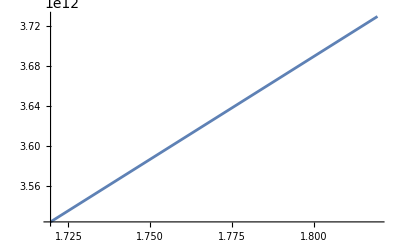

```mathematica
Plot[net[i], {i, 1719532800000, 1819532800000}]
```

```mathematica
filename="C:\\Users\\chris\\Downloads\\market_groups.json";
d=Dataset[Association/@Import[filename]]
```

Dataset[<>]

```mathematica
marketGroupName=(d[[All, 3]]//Normal)[[;;20]]
marketGroupID=(d[[All, 1]]//Normal)[[;;20]]
marketGoupAssociation=AssociationThread[marketGroupName, marketGroupID]
```

{Blueprints & Reactions,Ships,Standard Frigates,Standard Cruisers,Standard Battleships,Standard Haulers,Ship Equipment,Turrets & Launchers,Ammunition & Charges,Hull & Armor,Trade Goods,Industrial Goods,Radioactive Goods,Passengers,Implants & Boosters,Implants,Propulsion,Standard Ores,Caldari,Minmatar}

```mathematica
%1325 //InputForm
```

{"Blueprints & Reactions", "Ships", "Standard Frigates", "Standard Cruisers", "Standard Battleships", "Standard Haulers", "Ship Equipment", 
 "Turrets & Launchers", "Ammunition & Charges", "Hull & Armor", "Trade Goods", "Industrial Goods", "Radioactive Goods", "Passengers", 
 "Implants & Boosters", "Implants", "Propulsion", "Standard Ores", "Caldari", "Minmatar"}

```mathematica
Import["https://evetycoon.com/api/v1/market/history/10000002/44992"]
```

```mathematica
GOODGROUPID={1923}
TYPEID={44992, 33697, 21587, 23153, 23154, 23155, 23156, 23157, 23163, 20110, 21073, 21568, 21570};
mGroupID=1902
i=1;

a=Import["https://evetycoon.com/api/v1/market/groups/"<>ToString[mGroupID]<>"/types"]
a=a[[i]];
a=a[[1]];
b=a//Values;
c=Import["https://evetycoon.com/api/v1/market/history/10000002/"<>ToString[%]]
values=Values[c]
```

{1923}

1902

{{typeID→20110,groupID→530,typeName→Sleeper Foundation Block,iconID→2890,marketGroupID→1902,description→Alloys and special materials used in the manufacture of modules based on Ancient technology.,published→1,volume→1.},{typeID→21073,groupID→530,typeName→Sleeper Split Cables,iconID→2890,marketGroupID→1902,description→Alloys and special materials used in the manufacture of modules based on Ancient technology.,published→1,volume→1.},{typeID→21568,groupID→732,typeName→Sleeper Data Interface Protocol,iconID→2886,marketGroupID→1902,description→,published→1,volume→1.},{typeID→21569,groupID→732,typeName→Sleeper Profound Research Notes,iconID→2886,marketGroupID→1902,description→,published→1,volume→1.},{typeID→21570,groupID→732,typeName→Sleeper Manuscripts,iconID→2886,marketGroupID→1902,description→,published→1,volume→1.},{typeID→21571,groupID→732,typeName→Sleeper Technical Schematics,iconID→2886,marketGroupID→1902,description→,published→1,volume→1.},{typeID→21572,groupID→732,typeName→Sleeper Data Crystals,iconID→2886,marketGroupID→1902,description→,published→1,volume→1.},{typeID→21584,groupID→530,typeName→Sleeper Micro Circuits,iconID→2890,marketGroupID→1902,description→Alloys and special materials used in the manufacture of modules based on Ancient technology.,published→1,volume→1.},{typeID→21585,groupID→530,typeName→Sleeper Cryo Batteries,iconID→2890,marketGroupID→1902,description→Alloys and special materials used in the manufacture of modules based on Ancient technology.,published→1,volume→1.},{typeID→21586,groupID→530,typeName→Sleeper Virtual Energizer,iconID→2890,marketGroupID→1902,description→Alloys and special materials used in the manufacture of modules based on Ancient technology.,published→1,volume→1.},{typeID→21719,groupID→528,typeName→Sleeper Hyperbooster,iconID→2889,marketGroupID→1902,description→,published→1,volume→0.1},{typeID→21720,groupID→528,typeName→Sleeper Thermal Regulator,iconID→2889,marketGroupID→1902,description→,published→1,volume→0.1},{typeID→21721,groupID→528,typeName→Sleeper Heat Nullifying Coil,iconID→2889,marketGroupID→1902,description→,published→1,volume→0.1},{typeID→21722,groupID→528,typeName→Sleeper Nanite Cluster,iconID→2889,marketGroupID→1902,description→,published→1,volume→0.1},{typeID→21723,groupID→528,typeName→Sleeper Reintegration Control,iconID→2889,marketGroupID→1902,description→,published→1,volume→0.1}}

```mathematica
userChoice="Blueprints & Reactions";

marketGroupName=(d[[All, 3]]//Normal)[[;;20]];
marketGroupID=(d[[All, 1]]//Normal)[[;;20]];
marketGoupAssociation=AssociationThread[marketGroupName, marketGroupID];

mGroupID=Key[userChoice][marketGoupAssociation]
```

2

```mathematica
Import["https://evetycoon.com/api/v1/market/stats/10000002/44992"]
```

{buyVolume→501725,sellVolume→384228,buyOrders→351,sellOrders→168,buyOutliers→99,sellOutliers→8,buyThreshold→503400.,sellThreshold→5.184×10^7,buyAvgFivePercent→5.01405×10^6,sellAvgFivePercent→5.20689×10^6,maxBuy→5.034×10^6,minSell→5.184×10^6}

```mathematica
dataFromFuncIDIndex[i_]:=Module[{typeID,FullData},
typeID={44992, 33697, 21587, 23153, 23154, 23155, 23156, 23157, 23163, 20110, 21073, 21568}[[i]];
FullData=Import["https://evetycoon.com/api/v1/market/history/10000002/"<>ToString[typeID]];
Values[#[[1]]]->Values[#[[4]]]&/@FullData];
dataFromFuncIDIndex[1]  (* Can be from 1 - 12 *)
```

{1572566400000→3.47012×10^6,1572652800000→3.456×10^6,1572739200000→3.44944×10^6,1572825600000→3.47×10^6,1572912000000→3.45731×10^6,1572998400000→3.46×10^6,1573084800000→3.465×10^6,1573171200000→3.46033×10^6,1573257600000→3.45031×10^6,1573344000000→3.43167×10^6,1573430400000→3.44089×10^6,1573516800000→3.54285×10^6,1573603200000→3.4378×10^6,1573689600000→3.43274×10^6,1573776000000→3.4303×10^6,1573862400000→3.41201×10^6,1573948800000→3.40401×10^6,1574035200000→3.4037×10^6,1574121600000→3.40233×10^6,1574208000000→3.382×10^6,1574294400000→3.392×10^6,1574380800000→3.37703×10^6,1574467200000→3.36062×10^6,1574553600000→3.3462×10^6,1574640000000→3.375×10^6,1574726400000→3.35×10^6,1574812800000→3.44697×10^6,1574899200000→3.3×10^6,1574985600000→3.21315×10^6,1575072000000→3.252×10^6,1575158400000→3.2935×10^6,1575244800000→3.2752×10^6,1575331200000→3.3059×10^6,1575417600000→3.3073×10^6,1575504000000→3.30102×10^6,1575590400000→3.28302×10^6,1575676800000→3.2784×10^6,1575763200000→3.27207×10^6,1575849600000→3.31001×10^6,1575936000000→3.3637×10^6,1576022400000→3.3602×10^6,1576108800000→3.317×10^6,1576195200000→3.30761×10^6,1576281600000→3.29101×10^6,1576368000000→3.26815×10^6,1576454400000→3.25×10^6,1576540800000→3.2431×10^6,1576627200000→3.24009×10^6,1576713600000→3.21016×10^6,1576800000000→3.2046×10^6,1576886400000→3.171×10^6,1576972800000→3.1669×10^6,1577059200000→3.18×10^6,1577145600000→3.2102×10^6,1577232000000→3.39998×10^6,1577318400000→3.41127×10^6,1577404800000→3.3713×10^6,1577491200000→3.28×10^6,1577577600000→3.25209×10^6,1577664000000→3.25×10^6,1577750400000→3.23006×10^6,1577836800000→3.2101×10^6,1577923200000→3.18622×10^6,1578009600000→3.20001×10^6,1578096000000→3.19931×10^6,1578182400000→3.1922×10^6,1578268800000→3.1854×10^6,1578355200000→3.2×10^6,1578441600000→3.205×10^6,1578528000000→3.20121×10^6,1578614400000→3.20199×10^6,1578700800000→3.19171×10^6,1578787200000→3.2×10^6,1578873600000→3.195×10^6,1578960000000→3.19211×10^6,1579046400000→3.1972×10^6,1579132800000→3.1942×10^6,1579219200000→3.1931×10^6,1579305600000→3.19104×10^6,1579392000000→3.19635×10^6,1579478400000→3.20405×10^6,1579564800000→3.202×10^6,1579651200000→3.20762×10^6,1579737600000→3.21208×10^6,1579824000000→3.22594×10^6,1579910400000→3.28×10^6,1579996800000→3.27401×10^6,1580083200000→3.27621×10^6,1580169600000→3.29×10^6,1580256000000→3.2972×10^6,1580342400000→3.29525×10^6,1580428800000→3.2965×10^6,1580515200000→3.28061×10^6,1580601600000→3.28022×10^6,1580688000000→3.27955×10^6,1580774400000→3.27105×10^6,1580860800000→3.28603×10^6,1580947200000→3.276×10^6,1581033600000→3.26831×10^6,1581120000000→3.26403×10^6,1581206400000→3.2585×10^6,1581292800000→3.25614×10^6,1581379200000→3.263×10^6,1581465600000→3.30001×10^6,1581552000000→3.28051×10^6,1581638400000→3.27504×10^6,1581724800000→3.28471×10^6,1581811200000→3.27606×10^6,1581897600000→3.27814×10^6,1581984000000→3.28501×10^6,1582070400000→3.28312×10^6,1582156800000→3.2845×10^6,1582243200000→3.2803×10^6,1582329600000→3.25652×10^6,1582416000000→3.24601×10^6,1582502400000→3.35008×10^6,1582588800000→3.29501×10^6,1582675200000→3.28607×10^6,1582761600000→3.28606×10^6,1582848000000→3.20012×10^6,1582934400000→3.19002×10^6,1583020800000→3.18501×10^6,1583107200000→3.19341×10^6,1583193600000→3.206×10^6,1583280000000→3.22251×10^6,1583366400000→3.21706×10^6,1583452800000→3.19815×10^6,1583539200000→3.20025×10^6,1583625600000→3.20404×10^6,1583712000000→3.22016×10^6,1583798400000→3.22703×10^6,1583884800000→3.219×10^6,1583971200000→3.221×10^6,1584057600000→3.22×10^6,1584144000000→3.212×10^6,1584230400000→3.206×10^6,1584316800000→3.201×10^6,1584403200000→3.196×10^6,1584489600000→3.186×10^6,1584576000000→3.176×10^6,1584662400000→3.151×10^6,1584748800000→3.101×10^6,1584835200000→3.124×10^6,1584921600000→3.15×10^6,1585008000000→3.15×10^6,1585094400000→3.136×10^6,1585180800000→3.135×10^6,1585267200000→3.126×10^6,1585353600000→3.093×10^6,1585440000000→3.099×10^6,1585526400000→3.074×10^6,1585612800000→3.056×10^6,1585699200000→3.013×10^6,1585785600000→2.913×10^6,1585872000000→2.9×10^6,1585958400000→2.958×10^6,1586044800000→2.977×10^6,1586131200000→2.962×10^6,1586217600000→2.915×10^6,1586304000000→2.903×10^6,1586390400000→2.887×10^6,1586476800000→3.135×10^6,1586563200000→3.173×10^6,1586649600000→3.075×10^6,1586736000000→2.971×10^6,1586822400000→2.949×10^6,1586908800000→2.871×10^6,1586995200000→2.778×10^6,1587081600000→2.74×10^6,1587168000000→2.72×10^6,1587254400000→2.716×10^6,1587340800000→2.745×10^6,1587427200000→2.779×10^6,1587513600000→2.796×10^6,1587600000000→2.768×10^6,1587686400000→2.73×10^6,1587772800000→2.681×10^6,1587859200000→2.672×10^6,1587945600000→2.66×10^6,1588032000000→2.644×10^6,1588118400000→2.608×10^6,1588204800000→2.58×10^6,1588291200000→2.573×10^6,1588377600000→2.593×10^6,1588464000000→2.583×10^6,1588550400000→2.575×10^6,1588636800000→2.608×10^6,1588723200000→2.594×10^6,1588809600000→2.592×10^6,1588896000000→2.579×10^6,1588982400000→2.55×10^6,1589068800000→2.556×10^6,1589155200000→2.578×10^6,1589241600000→2.564×10^6,1589328000000→2.547×10^6,1589414400000→2.526×10^6,1589500800000→2.535×10^6,1589587200000→2.5×10^6,1589673600000→2.465×10^6,1589760000000→2.451×10^6,1589846400000→2.468×10^6,1589932800000→2.476×10^6,1590019200000→2.49×10^6,1590105600000→2.498×10^6,1590192000000→2.478×10^6,1590278400000→2.481×10^6,1590364800000→2.609×10^6,1590451200000→2.806×10^6,1590537600000→2.673×10^6,1590624000000→2.648×10^6,1590710400000→2.516×10^6,1590796800000→2.492×10^6,1590883200000→2.506×10^6,1590969600000→2.526×10^6,1591056000000→2.531×10^6,1591142400000→2.542×10^6,1591228800000→2.542×10^6,1591315200000→2.531×10^6,1591401600000→2.521×10^6,1591488000000→2.516×10^6,1591574400000→2.545×10^6,1591660800000→2.545×10^6,1591747200000→2.553×10^6,1591833600000→2.558×10^6,1591920000000→2.705×10^6,1592006400000→2.752×10^6,1592092800000→2.757×10^6,1592179200000→2.612×10^6,1592265600000→2.61×10^6,1592352000000→2.571×10^6,1592438400000→2.581×10^6,1592524800000→2.583×10^6,1592611200000→2.567×10^6,1592697600000→2.567×10^6,1592784000000→2.563×10^6,1592870400000→2.55×10^6,1592956800000→2.558×10^6,1593043200000→2.555×10^6,1593129600000→2.55×10^6,1593216000000→2.554×10^6,1593302400000→2.544×10^6,1593388800000→2.551×10^6,1593475200000→2.523×10^6,1593561600000→2.511×10^6,1593648000000→2.51×10^6,1593734400000→2.503×10^6,1593820800000→2.479×10^6,1593907200000→2.451×10^6,1593993600000→2.477×10^6,1594080000000→2.46×10^6,1594166400000→2.463×10^6,1594252800000→2.477×10^6,1594339200000→2.48×10^6,1594425600000→2.487×10^6,1594512000000→2.489×10^6,1594598400000→2.486×10^6,1594684800000→2.49×10^6,1594771200000→2.49×10^6,1594857600000→2.48×10^6,1594944000000→2.48×10^6,1595030400000→2.483×10^6,1595116800000→2.485×10^6,1595203200000→2.495×10^6,1595289600000→2.492×10^6,1595376000000→2.495×10^6,1595462400000→2.492×10^6,1595548800000→2.491×10^6,1595635200000→2.494×10^6,1595721600000→2.494×10^6,1595808000000→2.5×10^6,1595894400000→2.496×10^6,1595980800000→2.504×10^6,1596067200000→2.503×10^6,1596153600000→2.495×10^6,1596240000000→2.491×10^6,1596326400000→2.496×10^6,1596412800000→2.5×10^6,1596499200000→2.495×10^6,1596585600000→2.5×10^6,1596672000000→2.495×10^6,1596758400000→2.499×10^6,1596844800000→2.499×10^6,1596931200000→2.515×10^6,1597017600000→2.508×10^6,1597104000000→2.513×10^6,1597190400000→2.531×10^6,1597276800000→2.523×10^6,1597363200000→2.533×10^6,1597449600000→2.534×10^6,1597536000000→2.541×10^6,1597622400000→2.543×10^6,1597708800000→2.544×10^6,1597795200000→2.552×10^6,1597881600000→2.556×10^6,1597968000000→2.548×10^6,1598054400000→2.544×10^6,1598140800000→2.554×10^6,1598227200000→2.557×10^6,1598313600000→2.57×10^6,1598400000000→2.582×10^6,1598486400000→2.597×10^6,1598572800000→2.799×10^6,1598659200000→2.73×10^6,1598745600000→2.728×10^6,1598832000000→2.632×10^6,1598918400000→2.615×10^6,1599004800000→2.631×10^6,1599091200000→2.628×10^6,1599177600000→2.626×10^6,1599264000000→2.623×10^6,1599350400000→2.613×10^6,1599436800000→2.618×10^6,1599523200000→2.615×10^6,1599609600000→2.61×10^6,1599696000000→2.602×10^6,1599782400000→2.6×10^6,1599868800000→2.6×10^6,1599955200000→2.612×10^6,1600041600000→2.617×10^6,1600128000000→2.626×10^6,1600214400000→2.615×10^6,1600300800000→2.612×10^6,1600387200000→2.611×10^6,1600473600000→2.607×10^6,1600560000000→2.608×10^6,1600646400000→2.623×10^6,1600732800000→2.612×10^6,1600819200000→2.607×10^6,1600905600000→2.61×10^6,1600992000000→2.607×10^6,1601078400000→2.611×10^6,1601164800000→2.607×10^6,1601251200000→2.613×10^6,1601337600000→2.614×10^6,1601424000000→2.618×10^6,1601510400000→2.615×10^6,1601596800000→2.625×10^6,1601683200000→2.626×10^6,1601769600000→2.634×10^6,1601856000000→2.66×10^6,1601942400000→2.67×10^6,1602028800000→2.726×10^6,1602115200000→2.762×10^6,1602201600000→2.787×10^6,1602288000000→2.72×10^6,1602374400000→2.688×10^6,1602460800000→2.692×10^6,1602547200000→2.689×10^6,1602633600000→2.698×10^6,1602720000000→2.696×10^6,1602806400000→2.699×10^6,1602892800000→2.697×10^6,1602979200000→2.693×10^6,1603065600000→2.694×10^6,1603152000000→2.707×10^6,1603238400000→2.7×10^6,1603324800000→2.701×10^6,1603411200000→2.713×10^6,1603497600000→2.706×10^6,1603584000000→2.707×10^6,1603670400000→2.705×10^6,1603756800000→2.71×10^6,1603843200000→2.709×10^6,1603929600000→2.706×10^6,1604016000000→2.713×10^6,1604102400000→2.687×10^6,1604188800000→2.691×10^6,1604275200000→2.693×10^6,1604361600000→2.696×10^6,1604448000000→2.706×10^6,1604534400000→2.697×10^6,1604620800000→2.694×10^6,1604707200000→2.692×10^6,1604793600000→2.693×10^6,1604880000000→2.697×10^6,1604966400000→2.7×10^6,1605052800000→2.7×10^6,1605139200000→2.709×10^6,1605225600000→2.703×10^6,1605312000000→2.702×10^6,1605398400000→2.7×10^6,1605484800000→2.704×10^6,1605571200000→2.706×10^6,1605657600000→2.718×10^6,1605744000000→2.72×10^6,1605830400000→2.716×10^6,1605916800000→2.709×10^6,1606003200000→2.717×10^6,1606089600000→2.726×10^6,1606176000000→2.751×10^6,1606262400000→2.748×10^6,1606348800000→2.63×10^6,1606435200000→2.64×10^6,1606521600000→2.688×10^6,1606608000000→2.686×10^6,1606694400000→2.711×10^6,1606780800000→2.708×10^6,1606867200000→2.696×10^6,1606953600000→2.696×10^6,1607040000000→2.691×10^6,1607126400000→2.686×10^6,1607212800000→2.682×10^6,1607299200000→2.688×10^6,1607385600000→2.683×10^6,1607472000000→2.68×10^6,1607558400000→2.697×10^6,1607644800000→2.679×10^6,1607731200000→2.672×10^6,1607817600000→2.674×10^6,1607904000000→2.672×10^6,1607990400000→2.664×10^6,1608076800000→2.666×10^6,1608163200000→2.661×10^6,1608249600000→2.664×10^6,1608336000000→2.657×10^6,1608422400000→2.642×10^6,1608508800000→2.642×10^6,1608595200000→2.65×10^6,1608681600000→2.646×10^6,1608768000000→2.8×10^6,1608854400000→2.819×10^6,1608940800000→2.77×10^6,1609027200000→2.657×10^6,1609113600000→2.651×10^6,1609200000000→2.647×10^6,1609286400000→2.643×10^6,1609372800000→2.638×10^6,1609459200000→2.606×10^6,1609545600000→2.56×10^6,1609632000000→2.552×10^6,1609718400000→2.559×10^6,1609804800000→2.557×10^6,1609891200000→2.546×10^6,1609977600000→2.541×10^6,1610064000000→2.533×10^6,1610150400000→2.492×10^6,1610236800000→2.49×10^6,1610323200000→2.512×10^6,1610409600000→2.5×10^6,1610496000000→2.531×10^6,1610582400000→2.508×10^6,1610668800000→2.501×10^6,1610755200000→2.499×10^6,1610841600000→2.503×10^6,1610928000000→2.505×10^6,1611014400000→2.5×10^6,1611100800000→2.501×10^6,1611187200000→2.498×10^6,1611273600000→2.49×10^6,1611360000000→2.486×10^6,1611446400000→2.481×10^6,1611532800000→2.481×10^6,1611619200000→2.484×10^6,1611705600000→2.473×10^6,1611792000000→2.472×10^6,1611878400000→2.471×10^6,1611964800000→2.466×10^6,1612051200000→2.455×10^6,1612137600000→2.475×10^6,1612224000000→2.459×10^6,1612310400000→2.455×10^6,1612396800000→2.446×10^6,1612483200000→2.442×10^6,1612569600000→2.439×10^6,1612656000000→2.438×10^6,1612742400000→2.46×10^6,1612828800000→2.445×10^6,1612915200000→2.444×10^6,1613001600000→2.441×10^6,1613088000000→2.438×10^6,1613174400000→2.43×10^6,1613260800000→2.427×10^6,1613347200000→2.414×10^6,1613433600000→2.413×10^6,1613520000000→2.412×10^6,1613606400000→2.41×10^6,1613692800000→2.41×10^6,1613779200000→2.4×10^6,1613865600000→2.408×10^6,1613952000000→2.415×10^6,1614038400000→2.418×10^6,1614124800000→2.421×10^6,1614211200000→2.42×10^6,1614297600000→2.402×10^6,1614384000000→2.362×10^6,1614470400000→2.335×10^6,1614556800000→2.334×10^6,1614643200000→2.338×10^6,1614729600000→2.337×10^6,1614816000000→2.341×10^6,1614902400000→2.343×10^6,1614988800000→2.331×10^6,1615075200000→2.322×10^6,1615161600000→2.33×10^6,1615248000000→2.324×10^6,1615334400000→2.318×10^6,1615420800000→2.317×10^6,1615507200000→2.315×10^6,1615593600000→2.301×10^6,1615680000000→2.298×10^6,1615766400000→2.305×10^6,1615852800000→2.304×10^6,1615939200000→2.291×10^6,1616025600000→2.245×10^6,1616112000000→2.223×10^6,1616198400000→2.201×10^6,1616284800000→2.199×10^6,1616371200000→2.204×10^6,1616457600000→2.209×10^6,1616544000000→2.24×10^6,1616630400000→2.244×10^6,1616716800000→2.225×10^6,1616803200000→2.198×10^6,1616889600000→2.195×10^6,1616976000000→2.195×10^6,1617062400000→2.208×10^6,1617148800000→2.219×10^6,1617235200000→2.2×10^6,1617321600000→2.2×10^6,1617408000000→2.197×10^6,1617494400000→2.208×10^6,1617580800000→2.239×10^6,1617667200000→2.22×10^6,1617753600000→2.237×10^6,1617840000000→2.255×10^6,1617926400000→2.264×10^6,1618012800000→2.3×10^6,1618099200000→2.3×10^6,1618185600000→2.326×10^6,1618272000000→2.361×10^6,1618358400000→2.405×10^6,1618444800000→2.394×10^6,1618531200000→2.386×10^6,1618617600000→2.37×10^6,1618704000000→2.332×10^6,1618790400000→2.406×10^6,1618876800000→2.388×10^6,1618963200000→2.367×10^6,1619049600000→2.366×10^6,1619136000000→2.346×10^6,1619222400000→2.298×10^6,1619308800000→2.297×10^6,1619395200000→2.296×10^6,1619481600000→2.3×10^6,1619568000000→2.304×10^6,1619654400000→2.308×10^6,1619740800000→2.305×10^6,1619827200000→2.301×10^6,1619913600000→2.309×10^6,1620000000000→2.298×10^6,1620086400000→2.296×10^6,1620172800000→2.293×10^6,1620259200000→2.306×10^6,1620345600000→2.31×10^6,1620432000000→2.314×10^6,1620518400000→2.313×10^6,1620604800000→2.38×10^6,1620691200000→2.401×10^6,1620777600000→2.411×10^6,1620864000000→2.438×10^6,1620950400000→2.398×10^6,1621036800000→2.341×10^6,1621123200000→2.377×10^6,1621209600000→2.406×10^6,1621296000000→2.421×10^6,1621382400000→2.405×10^6,1621468800000→2.374×10^6,1621555200000→2.366×10^6,1621641600000→2.346×10^6,1621728000000→2.375×10^6,1621814400000→2.386×10^6,1621900800000→2.382×10^6,1621987200000→2.365×10^6,1622073600000→2.385×10^6,1622160000000→2.381×10^6,1622246400000→2.417×10^6,1622332800000→2.39×10^6,1622419200000→2.392×10^6,1622505600000→2.402×10^6,1622592000000→2.397×10^6,1622678400000→2.391×10^6,1622764800000→2.39×10^6,1622851200000→2.397×10^6,1622937600000→2.405×10^6,1623024000000→2.415×10^6,1623110400000→2.451×10^6,1623196800000→2.441×10^6,1623283200000→2.504×10^6,1623369600000→2.497×10^6,1623456000000→2.504×10^6,1623542400000→2.472×10^6,1623628800000→2.476×10^6,1623715200000→2.489×10^6,1623801600000→2.479×10^6,1623888000000→2.484×10^6,1623974400000→2.478×10^6,1624060800000→2.472×10^6,1624147200000→2.474×10^6,1624233600000→2.481×10^6,1624320000000→2.491×10^6,1624406400000→2.5×10^6,1624492800000→2.502×10^6,1624579200000→2.5×10^6,1624665600000→2.51×10^6,1624752000000→2.56×10^6,1624838400000→2.548×10^6,1624924800000→2.552×10^6,1625011200000→2.566×10^6,1625097600000→2.57×10^6,1625184000000→2.564×10^6,1625270400000→2.559×10^6,1625356800000→2.602×10^6,1625443200000→2.621×10^6,1625529600000→2.613×10^6,1625616000000→2.726×10^6,1625702400000→2.693×10^6,1625788800000→2.689×10^6,1625875200000→2.664×10^6,1625961600000→2.649×10^6,1626048000000→2.7×10^6,1626134400000→2.71×10^6,1626220800000→2.698×10^6,1626307200000→2.7×10^6,1626393600000→2.696×10^6,1626480000000→2.686×10^6,1626566400000→2.693×10^6,1626652800000→2.687×10^6,1626739200000→2.667×10^6,1626825600000→2.673×10^6,1626912000000→2.65×10^6,1626998400000→2.634×10^6,1627084800000→2.618×10^6,1627171200000→2.581×10^6,1627257600000→2.613×10^6,1627344000000→2.72×10^6,1627430400000→2.72×10^6,1627516800000→2.721×10^6,1627603200000→2.72×10^6,1627689600000→2.644×10^6,1627776000000→2.691×10^6,1627862400000→2.696×10^6,1627948800000→2.71×10^6,1628035200000→2.688×10^6,1628121600000→2.681×10^6,1628208000000→2.665×10^6,1628294400000→2.633×10^6,1628380800000→2.626×10^6,1628467200000→2.636×10^6,1628553600000→2.631×10^6,1628640000000→2.616×10^6,1628726400000→2.616×10^6,1628812800000→2.599×10^6,1628899200000→2.589×10^6,1628985600000→2.561×10^6,1629072000000→2.591×10^6,1629158400000→2.575×10^6,1629244800000→2.565×10^6,1629331200000→2.551×10^6,1629417600000→2.556×10^6,1629504000000→2.559×10^6,1629590400000→2.58×10^6,1629676800000→2.592×10^6,1629763200000→2.563×10^6,1629849600000→2.587×10^6,1629936000000→2.59×10^6,1630022400000→2.586×10^6,1630108800000→2.58×10^6,1630195200000→2.579×10^6,1630281600000→2.579×10^6,1630368000000→2.587×10^6,1630454400000→2.588×10^6,1630540800000→2.591×10^6,1630627200000→2.585×10^6,1630713600000→2.59×10^6,1630800000000→2.592×10^6,1630886400000→2.598×10^6,1630972800000→2.615×10^6,1631059200000→2.621×10^6,1631145600000→2.633×10^6,1631232000000→2.641×10^6,1631318400000→2.637×10^6,1631404800000→2.634×10^6,1631491200000→2.643×10^6,1631577600000→2.654×10^6,1631664000000→2.656×10^6,1631750400000→2.662×10^6,1631836800000→2.698×10^6,1631923200000→2.694×10^6,1632009600000→2.7×10^6,1632096000000→2.71×10^6,1632182400000→2.746×10^6,1632268800000→2.743×10^6,1632355200000→2.729×10^6,1632441600000→2.731×10^6,1632528000000→2.726×10^6,1632614400000→2.737×10^6,1632700800000→2.757×10^6,1632787200000→2.771×10^6,1632873600000→2.791×10^6,1632960000000→2.794×10^6,1633046400000→2.802×10^6,1633132800000→2.778×10^6,1633219200000→2.79×10^6,1633305600000→2.796×10^6,1633392000000→2.763×10^6,1633478400000→2.771×10^6,1633564800000→2.779×10^6,1633651200000→2.78×10^6,1633737600000→2.776×10^6,1633824000000→2.783×10^6,1633910400000→2.793×10^6,1633996800000→2.808×10^6,1634083200000→2.835×10^6,1634169600000→2.829×10^6,1634256000000→2.83×10^6,1634342400000→2.83×10^6,1634428800000→2.832×10^6,1634515200000→2.832×10^6,1634601600000→2.846×10^6,1634688000000→2.891×10^6,1634774400000→2.945×10^6,1634860800000→2.93×10^6,1634947200000→2.952×10^6,1635033600000→2.955×10^6,1635120000000→2.94×10^6,1635206400000→2.943×10^6,1635292800000→2.938×10^6,1635379200000→2.942×10^6,1635465600000→2.924×10^6,1635552000000→2.855×10^6,1635638400000→2.845×10^6,1635724800000→2.84×10^6,1635811200000→2.841×10^6,1635897600000→2.882×10^6,1635984000000→2.91×10^6,1636070400000→2.871×10^6,1636156800000→2.9×10^6,1636243200000→2.906×10^6,1636329600000→2.907×10^6,1636416000000→2.98×10^6,1636502400000→2.953×10^6,1636588800000→2.951×10^6,1636675200000→2.932×10^6,1636761600000→2.929×10^6,1636848000000→2.914×10^6,1636934400000→2.926×10^6,1637020800000→2.908×10^6,1637107200000→2.895×10^6,1637193600000→2.891×10^6,1637280000000→2.857×10^6,1637366400000→2.848×10^6,1637452800000→2.851×10^6,1637539200000→2.857×10^6,1637625600000→2.856×10^6,1637712000000→2.857×10^6,1637798400000→2.802×10^6,1637884800000→2.755×10^6,1637971200000→2.781×10^6,1638057600000→2.801×10^6,1638144000000→2.794×10^6,1638230400000→2.786×10^6,1638316800000→2.778×10^6,1638403200000→2.784×10^6,1638489600000→2.802×10^6,1638576000000→2.78×10^6,1638662400000→2.781×10^6,1638748800000→2.792×10^6,1638835200000→2.767×10^6,1638921600000→2.785×10^6,1639008000000→2.767×10^6,1639094400000→2.768×10^6,1639180800000→2.764×10^6,1639267200000→2.78×10^6,1639353600000→2.767×10^6,1639440000000→2.76×10^6,1639526400000→2.759×10^6,1639612800000→2.766×10^6,1639699200000→2.76×10^6,1639785600000→2.752×10^6,1639872000000→2.751×10^6,1639958400000→2.775×10^6,1640044800000→2.768×10^6,1640131200000→2.929×10^6,1640217600000→2.913×10^6,1640304000000→2.809×10^6,1640390400000→2.786×10^6,1640476800000→2.763×10^6,1640563200000→2.775×10^6,1640649600000→2.777×10^6,1640736000000→2.767×10^6,1640822400000→2.765×10^6,1640908800000→2.758×10^6,1640995200000→2.752×10^6,1641081600000→2.746×10^6,1641168000000→2.781×10^6,1641254400000→2.776×10^6,1641340800000→2.756×10^6,1641427200000→2.754×10^6,1641513600000→2.759×10^6,1641600000000→2.735×10^6,1641686400000→2.739×10^6,1641772800000→2.748×10^6,1641859200000→2.739×10^6,1641945600000→2.736×10^6,1642032000000→2.742×10^6,1642118400000→2.752×10^6,1642204800000→2.746×10^6,1642291200000→2.75×10^6,1642377600000→2.747×10^6,1642464000000→2.751×10^6,1642550400000→2.754×10^6,1642636800000→2.75×10^6,1642723200000→2.749×10^6,1642809600000→2.75×10^6,1642896000000→2.75×10^6,1642982400000→2.747×10^6,1643068800000→2.755×10^6,1643155200000→2.755×10^6,1643241600000→2.749×10^6,1643328000000→2.743×10^6,1643414400000→2.817×10^6,1643500800000→2.785×10^6,1643587200000→2.8×10^6,1643673600000→2.786×10^6,1643760000000→2.785×10^6,1643846400000→2.768×10^6,1643932800000→2.763×10^6,1644019200000→2.758×10^6,1644105600000→2.753×10^6,1644192000000→2.776×10^6,1644278400000→2.759×10^6,1644364800000→2.762×10^6,1644451200000→2.771×10^6,1644537600000→2.766×10^6,1644624000000→2.78×10^6,1644710400000→2.785×10^6,1644796800000→2.784×10^6,1644883200000→2.795×10^6,1644969600000→2.797×10^6,1645056000000→2.796×10^6,1645142400000→2.805×10^6,1645228800000→2.816×10^6,1645315200000→2.816×10^6,1645401600000→2.808×10^6,1645488000000→2.804×10^6,1645574400000→2.81×10^6,1645660800000→2.796×10^6,1645747200000→2.786×10^6,1645833600000→2.92×10^6,1645920000000→2.982×10^6,1646006400000→2.98×10^6,1646092800000→2.867×10^6,1646179200000→2.802×10^6,1646265600000→2.802×10^6,1646352000000→2.999×10^6,1646438400000→3.064×10^6,1646524800000→3.01×10^6,1646611200000→2.902×10^6,1646697600000→2.946×10^6,1646784000000→2.928×10^6,1646870400000→2.898×10^6,1646956800000→2.894×10^6,1647043200000→2.87×10^6,1647129600000→2.905×10^6,1647216000000→2.907×10^6,1647302400000→2.927×10^6,1647388800000→2.972×10^6,1647475200000→2.991×10^6,1647561600000→2.99×10^6,1647648000000→2.966×10^6,1647734400000→2.98×10^6,1647820800000→2.999×10^6,1647907200000→3.095×10^6,1647993600000→3.008×10^6,1648080000000→3.007×10^6,1648166400000→3.006×10^6,1648252800000→3.012×10^6,1648339200000→3.008×10^6,1648425600000→3.005×10^6,1648512000000→3.005×10^6,1648598400000→2.995×10^6,1648684800000→2.977×10^6,1648771200000→2.931×10^6,1648857600000→2.91×10^6,1648944000000→2.911×10^6,1649030400000→2.906×10^6,1649116800000→2.918×10^6,1649203200000→2.907×10^6,1649289600000→2.956×10^6,1649376000000→2.903×10^6,1649462400000→2.901×10^6,1649548800000→2.904×10^6,1649635200000→2.911×10^6,1649721600000→2.889×10^6,1649808000000→2.9×10^6,1649894400000→2.902×10^6,1649980800000→2.894×10^6,1650067200000→2.9×10^6,1650153600000→2.9×10^6,1650240000000→2.897×10^6,1650326400000→2.892×10^6,1650412800000→2.904×10^6,1650499200000→2.95×10^6,1650585600000→3.447×10^6,1650672000000→3.545×10^6,1650758400000→3.37×10^6,1650844800000→3.4×10^6,1650931200000→3.3×10^6,1651017600000→3.182×10^6,1651104000000→3.1×10^6,1651190400000→3.085×10^6,1651276800000→3.09×10^6,1651363200000→3.087×10^6,1651449600000→3.101×10^6,1651536000000→3.225×10^6,1651622400000→3.206×10^6,1651708800000→3.215×10^6,1651795200000→3.216×10^6,1651881600000→3.26×10^6,1651968000000→3.398×10^6,1652054400000→3.321×10^6,1652140800000→3.336×10^6,1652227200000→3.326×10^6,1652313600000→3.366×10^6,1652400000000→3.45×10^6,1652486400000→3.402×10^6,1652572800000→3.449×10^6,1652659200000→3.425×10^6,1652745600000→3.513×10^6,1652832000000→3.552×10^6,1652918400000→3.577×10^6,1653004800000→3.596×10^6,1653091200000→3.569×10^6,1653177600000→3.684×10^6,1653264000000→3.63×10^6,1653350400000→3.797×10^6,1653436800000→3.632×10^6,1653523200000→3.642×10^6,1653609600000→3.644×10^6,1653696000000→3.562×10^6,1653782400000→3.531×10^6,1653868800000→3.572×10^6,1653955200000→3.525×10^6,1654041600000→3.515×10^6,1654128000000→3.474×10^6,1654214400000→3.47×10^6,1654300800000→3.462×10^6,1654387200000→3.461×10^6,1654473600000→3.475×10^6,1654560000000→3.799×10^6,1654646400000→3.864×10^6,1654732800000→3.802×10^6,1654819200000→3.812×10^6,1654905600000→3.845×10^6,1654992000000→3.89×10^6,1655078400000→3.93×10^6,1655164800000→3.786×10^6,1655251200000→3.645×10^6,1655337600000→3.652×10^6,1655424000000→3.615×10^6,1655510400000→3.653×10^6,1655596800000→3.616×10^6,1655683200000→3.694×10^6,1655769600000→3.692×10^6,1655856000000→3.666×10^6,1655942400000→3.722×10^6,1656028800000→3.7×10^6,1656115200000→3.686×10^6,1656201600000→3.659×10^6,1656288000000→3.645×10^6,1656374400000→3.677×10^6,1656460800000→3.665×10^6,1656547200000→3.649×10^6,1656633600000→3.634×10^6,1656720000000→3.648×10^6,1656806400000→3.655×10^6,1656892800000→3.665×10^6,1656979200000→3.721×10^6,1657065600000→3.688×10^6,1657152000000→3.705×10^6,1657238400000→3.681×10^6,1657324800000→3.689×10^6,1657411200000→3.7×10^6,1657497600000→3.75×10^6,1657584000000→3.92×10^6,1657670400000→3.778×10^6,1657756800000→3.78×10^6,1657843200000→3.78×10^6,1657929600000→3.766×10^6,1658016000000→3.801×10^6,1658102400000→3.816×10^6,1658188800000→3.8×10^6,1658275200000→3.81×10^6,1658361600000→3.808×10^6,1658448000000→3.833×10^6,1658534400000→3.821×10^6,1658620800000→3.855×10^6,1658707200000→3.877×10^6,1658793600000→3.952×10^6,1658880000000→3.929×10^6,1658966400000→3.91×10^6,1659052800000→3.911×10^6,1659139200000→3.954×10^6,1659225600000→3.95×10^6,1659312000000→3.931×10^6,1659398400000→3.961×10^6,1659484800000→4.002×10^6,1659571200000→4.087×10^6,1659657600000→4.082×10^6,1659744000000→4.069×10^6,1659830400000→4.114×10^6,1659916800000→4.116×10^6,1660003200000→4.12×10^6,1660089600000→4.131×10^6,1660176000000→4.146×10^6,1660262400000→4.134×10^6,1660348800000→4.17×10^6,1660435200000→4.162×10^6,1660521600000→4.183×10^6,1660608000000→4.212×10^6,1660694400000→4.184×10^6,1660780800000→4.207×10^6,1660867200000→4.216×10^6,1660953600000→4.5×10^6,1661040000000→4.604×10^6,1661126400000→4.507×10^6,1661212800000→4.459×10^6,1661299200000→4.447×10^6,1661385600000→4.448×10^6,1661472000000→4.461×10^6,1661558400000→4.434×10^6,1661644800000→4.433×10^6,1661731200000→4.471×10^6,1661817600000→4.439×10^6,1661904000000→4.446×10^6,1661990400000→4.433×10^6,1662076800000→4.5×10^6,1662163200000→4.446×10^6,1662249600000→4.459×10^6,1662336000000→4.45×10^6,1662422400000→4.465×10^6,1662508800000→4.464×10^6,1662595200000→4.471×10^6,1662681600000→4.463×10^6,1662768000000→4.36×10^6,1662854400000→4.373×10^6,1662940800000→4.394×10^6,1663027200000→4.407×10^6,1663113600000→4.428×10^6,1663200000000→4.443×10^6,1663286400000→4.451×10^6,1663372800000→4.469×10^6,1663459200000→4.457×10^6,1663545600000→4.485×10^6,1663632000000→4.561×10^6,1663718400000→4.5×10^6,1663804800000→4.53×10^6,1663891200000→5.44×10^6,1663977600000→5.32×10^6,1664064000000→5.275×10^6,1664150400000→5.175×10^6,1664236800000→4.622×10^6,1664323200000→4.627×10^6,1664409600000→4.604×10^6,1664496000000→4.502×10^6,1664582400000→4.42×10^6,1664668800000→4.39×10^6,1664755200000→4.405×10^6,1664841600000→4.415×10^6,1664928000000→4.422×10^6,1665014400000→4.634×10^6,1665100800000→4.524×10^6,1665187200000→4.437×10^6,1665273600000→4.446×10^6,1665360000000→4.433×10^6,1665446400000→4.471×10^6,1665532800000→4.462×10^6,1665619200000→4.5×10^6,1665705600000→4.485×10^6,1665792000000→4.464×10^6,1665878400000→4.499×10^6,1665964800000→4.521×10^6,1666051200000→4.509×10^6,1666137600000→4.525×10^6,1666224000000→4.663×10^6,1666310400000→4.681×10^6,1666396800000→4.661×10^6,1666483200000→4.732×10^6,1666569600000→4.851×10^6,1666656000000→4.92×10^6,1666742400000→4.873×10^6,1666828800000→4.877×10^6,1666915200000→4.841×10^6,1667001600000→4.7×10^6,1667088000000→4.715×10^6,1667174400000→4.853×10^6,1667260800000→4.9×10^6,1667347200000→4.805×10^6,1667433600000→4.812×10^6,1667520000000→4.782×10^6,1667606400000→4.788×10^6,1667692800000→4.857×10^6,1667779200000→4.851×10^6,1667865600000→4.812×10^6,1667952000000→4.814×10^6,1668038400000→4.78×10^6,1668124800000→4.755×10^6,1668211200000→4.771×10^6,1668297600000→4.802×10^6,1668384000000→4.784×10^6,1668470400000→4.903×10^6,1668556800000→4.9×10^6,1668643200000→4.905×10^6,1668729600000→4.88×10^6,1668816000000→4.853×10^6,1668902400000→4.881×10^6,1668988800000→4.959×10^6,1669075200000→4.965×10^6,1669161600000→4.907×10^6,1669248000000→4.91×10^6,1669334400000→4.901×10^6,1669420800000→4.894×10^6,1669507200000→4.955×10^6,1669593600000→4.9×10^6,1669680000000→4.805×10^6,1669766400000→4.81×10^6,1669852800000→4.814×10^6,1669939200000→4.79×10^6,1670025600000→4.797×10^6,1670112000000→4.796×10^6,1670198400000→4.8×10^6,1670284800000→4.802×10^6,1670371200000→4.81×10^6,1670457600000→4.808×10^6,1670544000000→4.791×10^6,1670630400000→4.775×10^6,1670716800000→4.8×10^6,1670803200000→4.753×10^6,1670889600000→4.731×10^6,1670976000000→4.753×10^6,1671062400000→4.77×10^6,1671148800000→4.695×10^6,1671235200000→4.624×10^6,1671321600000→4.623×10^6,1671408000000→4.615×10^6,1671494400000→4.611×10^6,1671580800000→4.623×10^6,1671667200000→4.625×10^6,1671753600000→4.605×10^6,1671840000000→4.615×10^6,1671926400000→4.619×10^6,1672012800000→4.662×10^6,1672099200000→4.622×10^6,1672185600000→4.626×10^6,1672272000000→4.622×10^6,1672358400000→4.62×10^6,1672444800000→4.588×10^6,1672531200000→4.573×10^6,1672617600000→4.643×10^6,1672704000000→4.617×10^6,1672790400000→4.607×10^6,1672876800000→4.601×10^6,1672963200000→4.657×10^6,1673049600000→4.623×10^6,1673136000000→4.62×10^6,1673222400000→4.63×10^6,1673308800000→4.99×10^6,1673395200000→5.176×10^6,1673481600000→5.089×10^6,1673568000000→5.046×10^6,1673654400000→5.054×10^6,1673740800000→5.031×10^6,1673827200000→5.05×10^6,1673913600000→5.182×10^6,1674000000000→5.395×10^6,1674086400000→5.295×10^6,1674172800000→4.875×10^6,1674259200000→4.716×10^6,1674345600000→4.672×10^6,1674432000000→4.712×10^6,1674518400000→4.727×10^6,1674604800000→4.752×10^6,1674691200000→4.78×10^6,1674777600000→5.08×10^6,1674864000000→5.1×10^6,1674950400000→4.98×10^6,1675036800000→5.01×10^6,1675123200000→4.981×10^6,1675209600000→4.941×10^6,1675296000000→4.934×10^6,1675382400000→4.951×10^6,1675468800000→4.852×10^6,1675555200000→4.835×10^6,1675641600000→4.856×10^6,1675728000000→4.83×10^6,1675814400000→4.9×10^6,1675900800000→4.83×10^6,1675987200000→4.792×10^6,1676073600000→4.865×10^6,1676160000000→4.789×10^6,1676246400000→4.802×10^6,1676332800000→4.745×10^6,1676419200000→4.792×10^6,1676505600000→4.78×10^6,1676592000000→4.72×10^6,1676678400000→4.7×10^6,1676764800000→4.7×10^6,1676851200000→4.7×10^6,1676937600000→4.7×10^6,1677024000000→4.642×10^6,1677110400000→4.628×10^6,1677196800000→4.887×10^6,1677283200000→4.869×10^6,1677369600000→4.763×10^6,1677456000000→4.8×10^6,1677542400000→4.721×10^6,1677628800000→4.634×10^6,1677715200000→4.624×10^6,1677801600000→4.61×10^6,1677888000000→4.566×10^6,1677974400000→4.527×10^6,1678060800000→4.558×10^6,1678147200000→4.531×10^6,1678233600000→4.467×10^6,1678320000000→4.46×10^6,1678406400000→4.423×10^6,1678492800000→4.36×10^6,1678579200000→4.335×10^6,1678665600000→4.385×10^6,1678752000000→4.397×10^6,1678838400000→4.389×10^6,1678924800000→4.37×10^6,1679011200000→4.359×10^6,1679097600000→4.342×10^6,1679184000000→4.375×10^6,1679270400000→4.338×10^6,1679356800000→4.328×10^6,1679443200000→4.368×10^6,1679529600000→4.321×10^6,1679616000000→4.349×10^6,1679702400000→4.35×10^6,1679788800000→4.381×10^6,1679875200000→4.33×10^6,1679961600000→4.413×10^6,1680048000000→4.38×10^6,1680134400000→4.4×10^6,1680220800000→4.404×10^6,1680307200000→4.396×10^6,1680393600000→4.486×10^6,1680480000000→4.438×10^6,1680566400000→4.431×10^6,1680652800000→4.414×10^6,1680739200000→4.431×10^6,1680825600000→4.44×10^6,1680912000000→4.424×10^6,1680998400000→4.422×10^6,1681084800000→4.41×10^6,1681171200000→4.422×10^6,1681257600000→4.435×10^6,1681344000000→4.398×10^6,1681430400000→4.389×10^6,1681516800000→4.368×10^6,1681603200000→4.344×10^6,1681689600000→4.332×10^6,1681776000000→4.391×10^6,1681862400000→4.366×10^6,1681948800000→4.439×10^6,1682035200000→4.392×10^6,1682121600000→4.41×10^6,1682208000000→4.4×10^6,1682294400000→4.415×10^6,1682380800000→4.482×10^6,1682467200000→4.45×10^6,1682553600000→4.482×10^6,1682640000000→4.48×10^6,1682726400000→4.48×10^6,1682812800000→4.472×10^6,1682899200000→4.593×10^6,1682985600000→4.544×10^6,1683072000000→4.501×10^6,1683158400000→4.6×10^6,1683244800000→4.605×10^6,1683331200000→4.6×10^6,1683417600000→4.575×10^6,1683504000000→4.619×10^6,1683590400000→4.6×10^6,1683676800000→4.532×10^6,1683763200000→4.511×10^6,1683849600000→4.492×10^6,1683936000000→4.455×10^6,1684022400000→4.462×10^6,1684108800000→4.455×10^6,1684195200000→4.46×10^6,1684281600000→4.457×10^6,1684368000000→4.47×10^6,1684454400000→4.45×10^6,1684540800000→4.47×10^6,1684627200000→4.551×10^6,1684713600000→4.478×10^6,1684800000000→4.473×10^6,1684886400000→4.5×10^6,1684972800000→4.471×10^6,1685059200000→4.455×10^6,1685145600000→4.459×10^6,1685232000000→4.5×10^6,1685318400000→4.51×10^6,1685404800000→4.57×10^6,1685491200000→4.502×10^6,1685577600000→4.475×10^6,1685664000000→5.386×10^6,1685750400000→5.39×10^6,1685836800000→5.511×10^6,1685923200000→5.722×10^6,1686009600000→5.727×10^6,1686096000000→5.×10^6,1686182400000→4.768×10^6,1686268800000→4.792×10^6,1686355200000→4.791×10^6,1686441600000→4.713×10^6,1686528000000→4.81×10^6,1686614400000→4.693×10^6,1686700800000→4.695×10^6,1686787200000→4.66×10^6,1686873600000→5.013×10^6,1686960000000→4.842×10^6,1687046400000→4.885×10^6,1687132800000→4.989×10^6,1687219200000→4.837×10^6,1687305600000→4.823×10^6,1687392000000→4.809×10^6,1687478400000→5.06×10^6,1687564800000→5.02×10^6,1687651200000→4.998×10^6,1687737600000→5.078×10^6,1687824000000→4.908×10^6,1687910400000→4.833×10^6,1687996800000→4.832×10^6,1688083200000→4.78×10^6,1688169600000→4.769×10^6,1688256000000→4.755×10^6,1688342400000→4.735×10^6,1688428800000→4.695×10^6,1688515200000→4.649×10^6,1688601600000→4.662×10^6,1688688000000→4.71×10^6,1688774400000→4.692×10^6,1688860800000→4.735×10^6,1688947200000→4.732×10^6,1689033600000→4.742×10^6,1689120000000→4.701×10^6,1689206400000→4.702×10^6,1689292800000→4.7×10^6,1689379200000→4.683×10^6,1689465600000→4.688×10^6,1689552000000→4.71×10^6,1689638400000→4.704×10^6,1689724800000→4.704×10^6,1689811200000→4.715×10^6,1689897600000→4.733×10^6,1689984000000→4.71×10^6,1690070400000→4.756×10^6,1690156800000→4.75×10^6,1690243200000→4.737×10^6,1690329600000→4.742×10^6,1690416000000→4.734×10^6,1690502400000→4.735×10^6,1690588800000→4.75×10^6,1690675200000→4.75×10^6,1690761600000→4.801×10^6,1690848000000→4.787×10^6,1690934400000→4.783×10^6,1691020800000→4.776×10^6,1691107200000→4.78×10^6,1691193600000→4.776×10^6,1691280000000→4.792×10^6,1691366400000→4.774×10^6,1691452800000→4.805×10^6,1691539200000→4.793×10^6,1691625600000→4.829×10^6,1691712000000→4.805×10^6,1691798400000→4.798×10^6,1691884800000→4.79×10^6,1691971200000→4.8×10^6,1692057600000→4.785×10^6,1692144000000→4.785×10^6,1692230400000→4.774×10^6,1692316800000→4.763×10^6,1692403200000→4.74×10^6,1692489600000→4.741×10^6,1692576000000→4.75×10^6,1692662400000→4.778×10^6,1692748800000→4.976×10^6,1692835200000→4.997×10^6,1692921600000→4.871×10^6,1693008000000→4.891×10^6,1693094400000→4.95×10^6,1693180800000→5.×10^6,1693267200000→4.765×10^6,1693353600000→4.762×10^6,1693440000000→4.784×10^6,1693699200000→4.771×10^6,1693785600000→4.774×10^6,1693872000000→4.783×10^6,1693958400000→4.778×10^6,1694044800000→4.772×10^6,1694131200000→4.766×10^6,1694217600000→4.769×10^6,1694304000000→4.78×10^6,1694390400000→4.794×10^6,1694476800000→4.801×10^6,1694563200000→4.8×10^6,1694649600000→4.835×10^6,1694736000000→4.802×10^6,1694822400000→4.773×10^6,1694908800000→4.785×10^6,1694995200000→4.785×10^6,1695081600000→4.804×10^6,1695168000000→4.803×10^6,1695254400000→4.998×10^6,1695340800000→4.837×10^6,1695427200000→4.806×10^6,1695513600000→4.803×10^6,1695600000000→4.83×10^6,1695686400000→4.85×10^6,1695772800000→4.828×10^6,1695859200000→4.819×10^6,1695945600000→4.82×10^6,1696032000000→4.814×10^6,1696118400000→4.805×10^6,1696204800000→4.813×10^6,1696291200000→4.85×10^6,1696377600000→4.865×10^6,1696464000000→4.9×10^6,1696550400000→4.93×10^6,1696636800000→4.853×10^6,1696723200000→4.847×10^6,1696809600000→4.851×10^6,1696896000000→4.861×10^6,1696982400000→4.845×10^6,1697068800000→4.851×10^6,1697155200000→5.1×10^6,1697241600000→5.1×10^6,1697328000000→4.958×10^6,1697414400000→4.975×10^6,1697500800000→5.098×10^6,1697587200000→4.825×10^6,1697673600000→4.85×10^6,1697760000000→4.814×10^6,1697846400000→4.809×10^6,1697932800000→4.802×10^6,1698019200000→4.836×10^6,1698105600000→4.833×10^6,1698192000000→4.829×10^6,1698278400000→4.836×10^6,1698364800000→4.852×10^6,1698451200000→4.868×10^6,1698537600000→4.891×10^6,1698624000000→4.904×10^6,1698710400000→4.92×10^6,1698796800000→4.912×10^6,1698883200000→4.911×10^6,1698969600000→4.879×10^6,1699056000000→4.808×10^6,1699142400000→4.81×10^6,1699228800000→4.838×10^6,1699315200000→4.859×10^6,1699401600000→4.832×10^6,1699488000000→4.821×10^6,1699574400000→4.828×10^6,1699660800000→4.841×10^6,1699747200000→4.854×10^6,1699833600000→4.848×10^6,1699920000000→4.875×10^6,1700006400000→4.831×10^6,1700092800000→4.814×10^6,1700179200000→4.812×10^6,1700265600000→4.815×10^6,1700352000000→4.815×10^6,1700438400000→4.818×10^6,1700524800000→4.892×10^6,1700611200000→4.833×10^6,1700697600000→4.85×10^6,1700784000000→4.845×10^6,1700870400000→4.853×10^6,1700956800000→4.876×10^6,1701043200000→4.819×10^6,1701129600000→4.796×10^6,1701216000000→4.81×10^6,1701302400000→4.796×10^6,1701388800000→4.789×10^6,1701475200000→4.912×10^6,1701561600000→5.033×10^6,1701648000000→4.95×10^6,1701734400000→4.857×10^6,1701820800000→4.858×10^6,1701907200000→4.85×10^6,1701993600000→4.818×10^6,1702080000000→4.81×10^6,1702166400000→4.823×10^6,1702252800000→4.845×10^6,1702339200000→4.832×10^6,1702425600000→4.848×10^6,1702512000000→4.841×10^6,1702598400000→4.83×10^6,1702684800000→4.82×10^6,1702771200000→4.827×10^6,1702857600000→4.835×10^6,1702944000000→4.878×10^6,1703030400000→4.86×10^6,1703116800000→4.9×10^6,1703203200000→4.882×10^6,1703289600000→4.842×10^6,1703376000000→4.846×10^6,1703462400000→4.852×10^6,1703548800000→4.863×10^6,1703635200000→4.851×10^6,1703721600000→4.889×10^6,1703808000000→4.88×10^6,1703894400000→4.871×10^6,1703980800000→4.871×10^6,1704067200000→4.87×10^6,1704153600000→4.897×10^6,1704240000000→4.9×10^6,1704326400000→4.885×10^6,1704412800000→4.867×10^6,1704499200000→4.856×10^6,1704585600000→4.892×10^6,1704672000000→4.891×10^6,1704758400000→4.895×10^6,1704844800000→4.864×10^6,1704931200000→4.847×10^6,1705017600000→4.828×10^6,1705104000000→4.84×10^6,1705190400000→4.844×10^6,1705276800000→4.842×10^6,1705363200000→4.844×10^6,1705449600000→4.867×10^6,1705536000000→4.87×10^6,1705622400000→4.875×10^6,1705708800000→4.842×10^6,1705795200000→4.857×10^6,1705881600000→4.858×10^6,1705968000000→4.885×10^6,1706054400000→4.881×10^6,1706140800000→4.871×10^6,1706227200000→4.86×10^6,1706313600000→4.831×10^6,1706400000000→4.844×10^6,1706486400000→4.825×10^6,1706572800000→4.815×10^6,1706659200000→4.852×10^6,1706745600000→4.835×10^6,1706832000000→4.824×10^6,1706918400000→4.838×10^6,1707004800000→4.836×10^6,1707091200000→4.882×10^6,1707177600000→4.874×10^6,1707264000000→5.1×10^6,1707350400000→5.24×10^6,1707436800000→5.2×10^6,1707523200000→5.194×10^6,1707609600000→5.199×10^6,1707696000000→5.237×10^6,1707782400000→5.231×10^6,1707868800000→4.915×10^6,1707955200000→4.897×10^6,1708041600000→4.904×10^6,1708128000000→4.884×10^6,1708214400000→4.904×10^6,1708300800000→4.902×10^6,1708387200000→4.914×10^6,1708473600000→4.873×10^6,1708560000000→4.847×10^6,1708646400000→4.843×10^6,1708732800000→4.84×10^6,1708819200000→4.85×10^6,1708905600000→4.865×10^6,1708992000000→4.857×10^6,1709078400000→4.858×10^6,1709164800000→4.854×10^6,1709251200000→4.85×10^6,1709337600000→4.847×10^6,1709424000000→4.865×10^6,1709510400000→4.86×10^6,1709596800000→4.88×10^6,1709683200000→4.897×10^6,1709769600000→4.875×10^6,1709856000000→4.891×10^6,1709942400000→4.887×10^6,1710028800000→4.88×10^6,1710115200000→4.887×10^6,1710201600000→4.874×10^6,1710288000000→4.87×10^6,1710374400000→4.874×10^6,1710460800000→4.89×10^6,1710547200000→4.883×10^6,1710633600000→4.903×10^6,1710720000000→4.903×10^6,1710806400000→4.927×10^6,1710892800000→4.89×10^6,1710979200000→4.925×10^6,1711065600000→4.901×10^6,1711152000000→4.915×10^6,1711238400000→4.944×10^6,1711324800000→4.908×10^6,1711411200000→4.922×10^6,1711497600000→4.922×10^6,1711584000000→4.93×10^6,1711670400000→4.906×10^6,1711756800000→4.951×10^6,1711843200000→4.934×10^6,1711929600000→4.946×10^6,1712016000000→5.005×10^6,1712102400000→5.×10^6,1712188800000→5.122×10^6,1712275200000→5.072×10^6,1712361600000→4.99×10^6,1712448000000→5.035×10^6,1712534400000→5.016×10^6,1712620800000→5.×10^6,1712707200000→4.91×10^6,1712793600000→4.913×10^6,1712880000000→4.91×10^6,1712966400000→4.91×10^6,1713052800000→4.909×10^6,1713139200000→4.92×10^6,1713225600000→4.922×10^6,1713312000000→4.96×10^6,1713398400000→4.979×10^6,1713484800000→4.99×10^6,1713571200000→5.02×10^6,1713657600000→4.994×10^6,1713744000000→5.247×10^6,1713830400000→5.019×10^6,1713916800000→5.015×10^6,1714003200000→5.009×10^6,1714089600000→5.018×10^6,1714176000000→5.041×10^6,1714262400000→5.057×10^6,1714348800000→5.124×10^6,1714435200000→5.088×10^6,1714521600000→5.07×10^6,1714608000000→4.999×10^6,1714694400000→4.945×10^6,1714780800000→4.927×10^6,1714867200000→4.967×10^6,1714953600000→4.967×10^6,1715040000000→4.955×10^6,1715126400000→4.951×10^6,1715212800000→4.942×10^6,1715299200000→4.963×10^6,1715385600000→4.992×10^6,1715472000000→4.979×10^6,1715558400000→5.×10^6,1715644800000→4.999×10^6,1715731200000→5.025×10^6,1715817600000→4.998×10^6,1715904000000→5.002×10^6,1715990400000→5.008×10^6,1716076800000→5.011×10^6,1716163200000→5.021×10^6,1716249600000→5.071×10^6,1716336000000→5.076×10^6,1716422400000→5.12×10^6,1716508800000→5.085×10^6,1716595200000→5.077×10^6,1716681600000→5.093×10^6,1716768000000→5.139×10^6,1716854400000→5.103×10^6,1716940800000→5.064×10^6,1717027200000→5.073×10^6,1717113600000→5.05×10^6,1717200000000→5.05×10^6,1717286400000→5.087×10^6,1717372800000→5.102×10^6,1717459200000→5.11×10^6,1717545600000→5.127×10^6,1717632000000→5.103×10^6,1717718400000→5.112×10^6,1717804800000→5.12×10^6,1717891200000→5.183×10^6,1717977600000→5.174×10^6,1718064000000→5.16×10^6,1718150400000→5.088×10^6,1718236800000→5.×10^6,1718323200000→4.948×10^6,1718409600000→4.958×10^6,1718496000000→4.963×10^6,1718582400000→4.982×10^6,1718668800000→5.03×10^6,1718755200000→5.015×10^6,1718841600000→5.049×10^6,1718928000000→5.092×10^6,1719014400000→5.072×10^6,1719100800000→5.077×10^6,1719187200000→5.001×10^6,1719273600000→5.005×10^6,1719360000000→5.016×10^6,1719446400000→5.187×10^6,1719532800000→5.111×10^6,1719619200000→5.157×10^6,1719705600000→5.174×10^6,1719792000000→5.2×10^6,1719878400000→5.061×10^6}

```mathematica
dataFromFuncIDIndex[i_]:=Module[{typeID,FullData},typeID={44992,33697,21587,23153,23154,23155,23156,23157,23163,20110,21073,21568}[[i]];
FullData=Import["https://evetycoon.com/api/v1/market/history/10000002/"<>ToString[typeID]];
Values[#[[1]]]->Values[#[[4]]]&/@FullData];
data=Standardize[dataFromFuncIDIndex[1]//Values];
data
Length[data]
```

{-0.153202,-0.167126,-0.173593,-0.15332,-0.16584,-0.163181,-0.158251,-0.162857,-0.17274,-0.191121,-0.182028,-0.0814757,-0.185072,-0.190069,-0.192469,-0.210506,-0.218404,-0.218708,-0.220055,-0.240105,-0.230244,-0.245007,-0.261191,-0.275411,-0.247009,-0.271664,-0.176031,-0.320974,-0.406625,-0.368312,-0.327384,-0.345434,-0.315154,-0.313772,-0.319973,-0.337724,-0.342276,-0.348517,-0.311102,-0.258153,-0.261603,-0.304209,-0.313473,-0.32984,-0.352384,-0.370284,-0.377088,-0.380057,-0.409574,-0.415055,-0.448194,-0.452237,-0.439318,-0.409535,-0.222376,-0.21124,-0.250654,-0.340698,-0.368222,-0.370284,-0.389948,-0.409633,-0.433182,-0.419582,-0.420278,-0.427284,-0.433992,-0.419594,-0.414663,-0.418403,-0.417631,-0.427772,-0.419594,-0.424524,-0.427379,-0.422353,-0.425312,-0.426399,-0.42843,-0.423194,-0.4156,-0.417621,-0.412079,-0.407684,-0.394013,-0.340695,-0.346604,-0.344436,-0.330834,-0.323733,-0.325657,-0.324426,-0.3401,-0.340481,-0.341142,-0.349524,-0.334751,-0.344643,-0.352231,-0.356448,-0.361901,-0.364229,-0.357463,-0.320969,-0.3402,-0.345586,-0.336053,-0.344584,-0.342532,-0.335757,-0.33762,-0.336256,-0.340399,-0.363853,-0.374219,-0.271585,-0.325899,-0.334716,-0.334722,-0.419475,-0.429432,-0.434377,-0.426096,-0.413677,-0.397399,-0.402769,-0.421414,-0.419345,-0.415608,-0.39971,-0.392935,-0.400856,-0.398884,-0.39987,-0.407759,-0.413677,-0.418608,-0.423539,-0.433401,-0.443263,-0.467918,-0.517228,-0.494545,-0.468904,-0.468904,-0.482711,-0.483697,-0.492573,-0.525117,-0.5192,-0.543855,-0.561606,-0.604013,-0.702633,-0.715453,-0.658254,-0.639516,-0.654309,-0.70066,-0.712495,-0.728274,-0.483697,-0.446221,-0.542869,-0.645433,-0.66713,-0.744053,-0.83577,-0.873245,-0.892969,-0.896914,-0.868314,-0.834783,-0.818018,-0.845632,-0.883107,-0.931431,-0.940307,-0.952141,-0.96792,-1.00342,-1.03104,-1.03794,-1.01822,-1.02808,-1.03597,-1.00342,-1.01723,-1.0192,-1.03202,-1.06062,-1.05471,-1.03301,-1.04682,-1.06358,-1.08429,-1.07542,-1.10993,-1.14445,-1.15826,-1.14149,-1.1336,-1.11979,-1.11191,-1.13163,-1.12867,-1.00244,-0.808156,-0.93932,-0.963975,-1.09415,-1.11782,-1.10402,-1.08429,-1.07936,-1.06851,-1.06851,-1.07936,-1.08922,-1.09415,-1.06555,-1.06555,-1.05766,-1.05273,-0.907762,-0.861411,-0.85648,-0.999479,-1.00145,-1.03991,-1.03005,-1.02808,-1.04386,-1.04386,-1.0478,-1.06062,-1.05273,-1.05569,-1.06062,-1.05668,-1.06654,-1.05964,-1.08725,-1.09908,-1.10007,-1.10697,-1.13064,-1.15826,-1.13262,-1.14938,-1.14642,-1.13262,-1.12966,-1.12275,-1.12078,-1.12374,-1.11979,-1.11979,-1.12966,-1.12966,-1.1267,-1.12473,-1.11486,-1.11782,-1.11486,-1.11782,-1.11881,-1.11585,-1.11585,-1.10993,-1.11388,-1.10599,-1.10697,-1.11486,-1.11881,-1.11388,-1.10993,-1.11486,-1.10993,-1.11486,-1.11092,-1.11092,-1.09514,-1.10204,-1.09711,-1.07936,-1.08725,-1.07739,-1.0764,-1.0695,-1.06753,-1.06654,-1.05865,-1.05471,-1.0626,-1.06654,-1.05668,-1.05372,-1.0409,-1.02906,-1.01427,-0.815059,-0.883107,-0.88508,-0.979755,-0.99652,-0.980741,-0.983699,-0.985672,-0.98863,-0.998492,-0.993561,-0.99652,-1.00145,-1.00934,-1.01131,-1.01131,-0.999479,-0.994548,-0.985672,-0.99652,-0.999479,-1.00046,-1.00441,-1.00342,-0.98863,-0.999479,-1.00441,-1.00145,-1.00441,-1.00046,-1.00441,-0.998492,-0.997506,-0.993561,-0.99652,-0.986658,-0.985672,-0.977782,-0.952141,-0.942279,-0.887052,-0.851549,-0.826894,-0.892969,-0.924528,-0.920583,-0.923541,-0.914666,-0.916638,-0.913679,-0.915652,-0.919597,-0.91861,-0.90579,-0.912693,-0.911707,-0.899873,-0.906776,-0.90579,-0.907762,-0.902831,-0.903817,-0.906776,-0.899873,-0.925514,-0.921569,-0.919597,-0.916638,-0.906776,-0.915652,-0.91861,-0.920583,-0.919597,-0.915652,-0.912693,-0.912693,-0.903817,-0.909735,-0.910721,-0.912693,-0.908748,-0.906776,-0.894942,-0.892969,-0.896914,-0.903817,-0.895928,-0.887052,-0.862397,-0.865356,-0.981727,-0.971865,-0.924528,-0.9265,-0.901845,-0.904804,-0.916638,-0.916638,-0.921569,-0.9265,-0.930445,-0.924528,-0.929458,-0.932417,-0.915652,-0.933403,-0.940307,-0.938334,-0.940307,-0.948196,-0.946224,-0.951155,-0.948196,-0.9551,-0.969893,-0.969893,-0.962003,-0.965948,-0.814073,-0.795336,-0.843659,-0.9551,-0.961017,-0.964962,-0.968906,-0.973837,-1.0054,-1.05076,-1.05865,-1.05175,-1.05372,-1.06457,-1.0695,-1.07739,-1.11782,-1.11979,-1.0981,-1.10993,-1.07936,-1.10204,-1.10895,-1.11092,-1.10697,-1.105,-1.10993,-1.10895,-1.11191,-1.11979,-1.12374,-1.12867,-1.12867,-1.12571,-1.13656,-1.13755,-1.13853,-1.14346,-1.15431,-1.13459,-1.15037,-1.15431,-1.16319,-1.16713,-1.17009,-1.17108,-1.14938,-1.16417,-1.16516,-1.16812,-1.17108,-1.17897,-1.18193,-1.19475,-1.19573,-1.19672,-1.19869,-1.19869,-1.20855,-1.20066,-1.19376,-1.1908,-1.18784,-1.18883,-1.20658,-1.24603,-1.27266,-1.27364,-1.2697,-1.27068,-1.26674,-1.26477,-1.2766,-1.28548,-1.27759,-1.2835,-1.28942,-1.29041,-1.29238,-1.30619,-1.30914,-1.30224,-1.30323,-1.31605,-1.36141,-1.38311,-1.40481,-1.40678,-1.40185,-1.39692,-1.36634,-1.3624,-1.38114,-1.40776,-1.41072,-1.41072,-1.3979,-1.38705,-1.40579,-1.40579,-1.40875,-1.3979,-1.36733,-1.38607,-1.3693,-1.35155,-1.34268,-1.30717,-1.30717,-1.28153,-1.24701,-1.20362,-1.21447,-1.22236,-1.23814,-1.27561,-1.20264,-1.22039,-1.2411,-1.24208,-1.26181,-1.30914,-1.31013,-1.31112,-1.30717,-1.30323,-1.29928,-1.30224,-1.30619,-1.2983,-1.30914,-1.31112,-1.31408,-1.30126,-1.29731,-1.29337,-1.29435,-1.22828,-1.20757,-1.1977,-1.17108,-1.21053,-1.26674,-1.23124,-1.20264,-1.18784,-1.20362,-1.23419,-1.24208,-1.26181,-1.23321,-1.22236,-1.2263,-1.24307,-1.22335,-1.22729,-1.19179,-1.21841,-1.21644,-1.20658,-1.21151,-1.21743,-1.21841,-1.21151,-1.20362,-1.19376,-1.15826,-1.16812,-1.10599,-1.11289,-1.10599,-1.13755,-1.1336,-1.12078,-1.13064,-1.12571,-1.13163,-1.13755,-1.13557,-1.12867,-1.11881,-1.10993,-1.10796,-1.10993,-1.10007,-1.05076,-1.0626,-1.05865,-1.04484,-1.0409,-1.04682,-1.05175,-1.00934,-0.990603,-0.998492,-0.887052,-0.919597,-0.923541,-0.948196,-0.962989,-0.912693,-0.902831,-0.914666,-0.912693,-0.916638,-0.9265,-0.919597,-0.925514,-0.945238,-0.93932,-0.962003,-0.977782,-0.993561,-1.03005,-0.998492,-0.892969,-0.892969,-0.891983,-0.892969,-0.96792,-0.921569,-0.916638,-0.902831,-0.924528,-0.931431,-0.94721,-0.978768,-0.985672,-0.97581,-0.980741,-0.995534,-0.995534,-1.0123,-1.02216,-1.04977,-1.02019,-1.03597,-1.04583,-1.05964,-1.05471,-1.05175,-1.03104,-1.0192,-1.0478,-1.02413,-1.02117,-1.02512,-1.03104,-1.03202,-1.03202,-1.02413,-1.02315,-1.02019,-1.02611,-1.02117,-1.0192,-1.01329,-0.99652,-0.990603,-0.978768,-0.970879,-0.974824,-0.977782,-0.968906,-0.958058,-0.956086,-0.950169,-0.914666,-0.91861,-0.912693,-0.902831,-0.867328,-0.870287,-0.884093,-0.882121,-0.887052,-0.876204,-0.85648,-0.842673,-0.822949,-0.81999,-0.812101,-0.83577,-0.823935,-0.818018,-0.850563,-0.842673,-0.834783,-0.833797,-0.837742,-0.830839,-0.820977,-0.806184,-0.779556,-0.785474,-0.784487,-0.784487,-0.782515,-0.782515,-0.768708,-0.724329,-0.671074,-0.685867,-0.664171,-0.661213,-0.676005,-0.673047,-0.677978,-0.674033,-0.691785,-0.759832,-0.769694,-0.774625,-0.773639,-0.733205,-0.705591,-0.744053,-0.715453,-0.709536,-0.70855,-0.636558,-0.663185,-0.665157,-0.683895,-0.686854,-0.701647,-0.689812,-0.707564,-0.720384,-0.724329,-0.75786,-0.766736,-0.763777,-0.75786,-0.758846,-0.75786,-0.812101,-0.858452,-0.832811,-0.813087,-0.81999,-0.82788,-0.83577,-0.829852,-0.812101,-0.833797,-0.832811,-0.821963,-0.846618,-0.828866,-0.846618,-0.845632,-0.849576,-0.833797,-0.846618,-0.853521,-0.854507,-0.847604,-0.853521,-0.861411,-0.862397,-0.838728,-0.845632,-0.686854,-0.702633,-0.805197,-0.82788,-0.850563,-0.838728,-0.836756,-0.846618,-0.84859,-0.855494,-0.861411,-0.867328,-0.832811,-0.837742,-0.857466,-0.859438,-0.854507,-0.878176,-0.874231,-0.865356,-0.874231,-0.87719,-0.871273,-0.861411,-0.867328,-0.863383,-0.866342,-0.862397,-0.859438,-0.863383,-0.864369,-0.863383,-0.863383,-0.866342,-0.858452,-0.858452,-0.864369,-0.870287,-0.797308,-0.828866,-0.814073,-0.82788,-0.828866,-0.845632,-0.850563,-0.855494,-0.860425,-0.837742,-0.854507,-0.851549,-0.842673,-0.847604,-0.833797,-0.828866,-0.829852,-0.819004,-0.817032,-0.818018,-0.809142,-0.798294,-0.798294,-0.806184,-0.810128,-0.804211,-0.818018,-0.82788,-0.695729,-0.634585,-0.636558,-0.747998,-0.812101,-0.812101,-0.61782,-0.553717,-0.606972,-0.713481,-0.670088,-0.68784,-0.717426,-0.721371,-0.745039,-0.710522,-0.70855,-0.688826,-0.644447,-0.625709,-0.626696,-0.650364,-0.636558,-0.61782,-0.523145,-0.608944,-0.60993,-0.610916,-0.604999,-0.608944,-0.611903,-0.611903,-0.621765,-0.639516,-0.684881,-0.705591,-0.704605,-0.709536,-0.697702,-0.70855,-0.660226,-0.712495,-0.714467,-0.711509,-0.704605,-0.726302,-0.715453,-0.713481,-0.721371,-0.715453,-0.715453,-0.718412,-0.723343,-0.711509,-0.666143,-0.176003,-0.0793554,-0.25194,-0.222354,-0.320974,-0.437345,-0.518214,-0.533007,-0.528076,-0.531034,-0.517228,-0.394939,-0.413677,-0.404801,-0.403815,-0.360422,-0.224327,-0.300264,-0.285471,-0.295333,-0.255885,-0.173044,-0.220382,-0.17403,-0.197699,-0.110914,-0.072452,-0.047797,-0.0290593,-0.0556866,0.0577262,0.00447147,0.169167,0.00644387,0.0163059,0.0182782,-0.06259,-0.0931622,-0.052728,-0.0990794,-0.108941,-0.149375,-0.15332,-0.16121,-0.162196,-0.148389,0.171139,0.235242,0.174098,0.18396,0.216504,0.260883,0.300331,0.158318,0.0192644,0.0261678,-0.0103215,0.027154,-0.00933531,0.0675882,0.0656158,0.0399746,0.0952017,0.0735054,0.0596986,0.0330712,0.0192644,0.0508228,0.0389884,0.0232092,0.00841627,0.022223,0.0291264,0.0389884,0.0942155,0.061671,0.0784364,0.0547676,0.0626572,0.0735054,0.122815,0.290469,0.150429,0.152401,0.152401,0.138594,0.173111,0.187904,0.172125,0.181987,0.180015,0.20467,0.192835,0.226366,0.248062,0.322027,0.299345,0.280607,0.281593,0.324,0.320055,0.301317,0.330903,0.371337,0.455164,0.450233,0.437413,0.481792,0.483764,0.487709,0.498557,0.51335,0.501516,0.537019,0.529129,0.549839,0.578439,0.550825,0.573508,0.582384,0.862464,0.965029,0.869368,0.82203,0.810196,0.811182,0.824002,0.797375,0.796389,0.833864,0.802306,0.809209,0.796389,0.862464,0.809209,0.82203,0.813154,0.827947,0.826961,0.833864,0.825975,0.724396,0.737217,0.757927,0.770748,0.791458,0.806251,0.81414,0.831892,0.820058,0.847671,0.922622,0.862464,0.89205,1.78949,1.67115,1.62677,1.52815,0.98278,0.987711,0.965029,0.864437,0.783568,0.753982,0.768775,0.778637,0.785541,0.994615,0.886133,0.800334,0.809209,0.796389,0.833864,0.824989,0.862464,0.847671,0.826961,0.861478,0.883174,0.87134,0.887119,1.02321,1.04097,1.02124,1.09126,1.20862,1.27667,1.23032,1.23426,1.19876,1.0597,1.0745,1.21059,1.25694,1.16325,1.17016,1.14057,1.14649,1.21454,1.20862,1.17016,1.17213,1.1386,1.11394,1.12972,1.1603,1.14254,1.2599,1.25694,1.26187,1.23722,1.21059,1.23821,1.31513,1.32105,1.26385,1.26681,1.25793,1.25103,1.31118,1.25694,1.16325,1.16819,1.17213,1.14846,1.15537,1.15438,1.15832,1.1603,1.16819,1.16621,1.14945,1.13367,1.15832,1.11197,1.09028,1.11197,1.12874,1.05477,0.984753,0.983767,0.975877,0.971932,0.983767,0.985739,0.966015,0.975877,0.979822,1.02223,0.98278,0.986725,0.98278,0.980808,0.94925,0.934457,1.00349,0.977849,0.967987,0.96207,1.0173,0.983767,0.980808,0.99067,1.3457,1.52913,1.44334,1.40093,1.40882,1.38614,1.40487,1.53505,1.74511,1.64649,1.23229,1.07548,1.03209,1.07154,1.08633,1.11099,1.1386,1.43446,1.45418,1.33584,1.36543,1.33683,1.29738,1.29047,1.30724,1.20961,1.19284,1.21355,1.18791,1.25694,1.18791,1.15043,1.22243,1.14748,1.1603,1.10408,1.15043,1.1386,1.07943,1.0597,1.0597,1.0597,1.0597,1.0025,0.988698,1.24412,1.22637,1.12183,1.15832,1.08041,0.994615,0.984753,0.970946,0.927553,0.889092,0.919664,0.893036,0.82992,0.823016,0.786527,0.724396,0.699741,0.749051,0.760886,0.752996,0.734258,0.72341,0.706645,0.739189,0.7027,0.692838,0.732286,0.685935,0.713548,0.714534,0.745107,0.69481,0.776665,0.74412,0.763844,0.767789,0.7599,0.848657,0.80132,0.794416,0.777651,0.794416,0.803292,0.787513,0.785541,0.773706,0.785541,0.798361,0.761872,0.752996,0.732286,0.708617,0.696783,0.754969,0.730314,0.802306,0.755955,0.773706,0.763844,0.778637,0.844713,0.813154,0.844713,0.84274,0.84274,0.834851,0.954181,0.905857,0.86345,0.961084,0.966015,0.961084,0.936429,0.979822,0.961084,0.894023,0.873312,0.854575,0.818085,0.824989,0.818085,0.823016,0.820058,0.832878,0.813154,0.832878,0.91276,0.840768,0.835837,0.862464,0.833864,0.818085,0.82203,0.862464,0.872326,0.931498,0.864437,0.837809,1.73624,1.74018,1.85951,2.0676,2.07253,1.35556,1.12677,1.15043,1.14945,1.07252,1.16819,1.0528,1.05477,1.02026,1.36838,1.19974,1.24215,1.34472,1.19481,1.18101,1.1672,1.41474,1.37529,1.35359,1.43249,1.26483,1.19087,1.18988,1.1386,1.12775,1.11394,1.09422,1.05477,1.00941,1.02223,1.06957,1.05181,1.09422,1.09126,1.10112,1.06069,1.06168,1.0597,1.04294,1.04787,1.06957,1.06365,1.06365,1.0745,1.09225,1.06957,1.11493,1.10901,1.09619,1.10112,1.09323,1.09422,1.10901,1.10901,1.15931,1.1455,1.14156,1.13465,1.1386,1.13465,1.15043,1.13268,1.16325,1.15142,1.18692,1.16325,1.15635,1.14846,1.15832,1.14353,1.14353,1.13268,1.12183,1.09915,1.10014,1.10901,1.13663,1.33189,1.3526,1.22834,1.24807,1.30625,1.35556,1.12381,1.12085,1.14254,1.12972,1.13268,1.14156,1.13663,1.13071,1.12479,1.12775,1.1386,1.15241,1.15931,1.15832,1.19284,1.1603,1.1317,1.14353,1.14353,1.16227,1.16128,1.35359,1.19481,1.16424,1.16128,1.18791,1.20763,1.18594,1.17706,1.17805,1.17213,1.16325,1.17114,1.20763,1.22243,1.25694,1.28653,1.21059,1.20468,1.20862,1.21848,1.2027,1.20862,1.45418,1.45418,1.31414,1.33091,1.45221,1.18298,1.20763,1.17213,1.1672,1.1603,1.19383,1.19087,1.18692,1.19383,1.20961,1.22539,1.24807,1.26089,1.27667,1.26878,1.26779,1.23623,1.16621,1.16819,1.1958,1.21651,1.18988,1.17903,1.18594,1.19876,1.21158,1.20566,1.23229,1.1889,1.17213,1.17016,1.17312,1.17312,1.17608,1.24905,1.19087,1.20763,1.2027,1.21059,1.23327,1.17706,1.15438,1.16819,1.15438,1.14748,1.26878,1.38811,1.30625,1.21454,1.21552,1.20763,1.17608,1.16819,1.18101,1.2027,1.18988,1.20566,1.19876,1.18791,1.17805,1.18495,1.19284,1.23525,1.2175,1.25694,1.23919,1.19974,1.20369,1.20961,1.22045,1.20862,1.2461,1.23722,1.22834,1.22834,1.22736,1.25398,1.25694,1.24215,1.2244,1.21355,1.24905,1.24807,1.25201,1.22144,1.20468,1.18594,1.19777,1.20172,1.19974,1.20172,1.2244,1.22736,1.23229,1.19974,1.21454,1.21552,1.24215,1.23821,1.22834,1.2175,1.1889,1.20172,1.18298,1.17312,1.20961,1.19284,1.18199,1.1958,1.19383,1.23919,1.2313,1.45418,1.59225,1.5528,1.54689,1.55182,1.58929,1.58338,1.27174,1.25398,1.26089,1.24116,1.26089,1.25892,1.27075,1.23032,1.20468,1.20073,1.19777,1.20763,1.22243,1.21454,1.21552,1.21158,1.20763,1.20468,1.22243,1.2175,1.23722,1.25398,1.23229,1.24807,1.24412,1.23722,1.24412,1.2313,1.22736,1.2313,1.24708,1.24018,1.2599,1.2599,1.28357,1.24708,1.2816,1.25793,1.27174,1.30034,1.26483,1.27864,1.27864,1.28653,1.26286,1.30724,1.29047,1.30231,1.36049,1.35556,1.47588,1.42657,1.3457,1.39008,1.37134,1.35556,1.26681,1.26976,1.26681,1.26681,1.26582,1.27667,1.27864,1.31612,1.33485,1.3457,1.37529,1.34965,1.59915,1.3743,1.37036,1.36444,1.37331,1.396,1.41178,1.47785,1.44235,1.4246,1.35458,1.30132,1.28357,1.32302,1.32302,1.31118,1.30724,1.29836,1.31907,1.34767,1.33485,1.35556,1.35458,1.38022,1.35359,1.35754,1.36345,1.36641,1.37627,1.42558,1.43051,1.47391,1.43939,1.4315,1.44728,1.49264,1.45714,1.41868,1.42756,1.40487,1.40487,1.44136,1.45616,1.46405,1.48081,1.45714,1.46602,1.47391,1.53604,1.52716,1.51336,1.44235,1.35556,1.30428,1.31414,1.31907,1.33781,1.38515,1.37036,1.40389,1.44629,1.42657,1.4315,1.35655,1.36049,1.37134,1.53998,1.46503,1.5104,1.52716,1.5528,1.41572}

1704

```mathematica
sequenceLength=9;

trainingData=Table[data[[i;;i+sequenceLength-1]],{i,1,Length[data]-sequenceLength}];

trainingLabels=data[[sequenceLength+1;;]];
```

```mathematica
net=NetChain[{LinearLayer[1000],Ramp,LinearLayer[1000],Ramp,LinearLayer[100],Ramp,LinearLayer[10],Ramp,LinearLayer[5],Ramp,LinearLayer[1]}]

trainingLabels=Total[trainingData,{2}];
trainedNet=NetTrain[net,trainingData->trainingLabels,Method->"SGD",LearningRate->0.01,MaxTrainingRounds->100]
testData=data[[-sequenceLength;;]];
predictedLabels=trainedNet[testData]
testData[[-1]]
```

NetChain[…]

NetChain[<11>]

0.130194

1.41572

{1.35655,1.36049,1.37134,1.53998,1.46503,1.5104,1.52716,1.5528,1.41572}

{1.35655,1.36049,1.37134,1.53998,1.46503,1.5104,1.52716,1.5528,1.41572,0.130194,0.130194,0.130194,0.130194,0.130194,0.130194,0.130194,0.130194,0.130194}

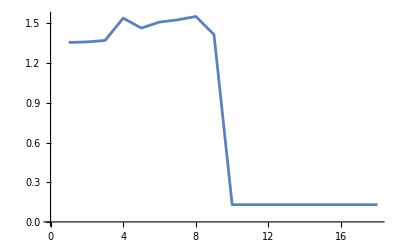

```mathematica
newData=data[[-sequenceLength;;]]
For[i=1,i<=sequenceLength,i++,
Drop[AppendTo[newData, trainedNet[data[[-sequenceLength;;]]]], -1]]
newData
ListLinePlot[newData]
```

```mathematica
randNums[n_List, amount_]:={#[[1]], #[[2]]+amount*RandomReal[]}&/@n
```

1.26844

```mathematica
TimeSeries["Values"]
```

TimeSeries::ntprs: The argument Values at position 1 is expected to be a list of time-value pairs or a list of states with equal dimensionality.

TimeSeries[Values]

TimeSeries[…]

{{1,2},{2,1},{5,6},{10,5},{12,7},{15,4}}

{{1,2.68265},{2,1.67817},{5,6.53167},{10,5.2638},{12,7.56696},{15,4.38705}}

TimeSeries[…]

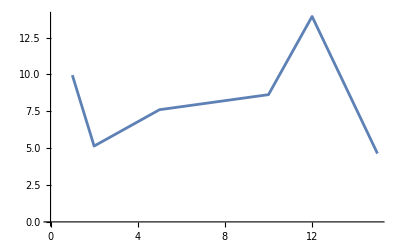

```mathematica
randNums[n_List, amount_]:=
v={2,1,6,5,7,4};
t={1,2,5,10,12,15};
ts=TimeSeries[v,{t}]
Normal[ts]
randNums[Normal[ts], 1]
TimeSeries[randNums[Normal[ts], 10]]
ListLinePlot[TimeSeries[%]]
```